# Results Fitting

```mathematica
ClearGlobal[]:=(ClearAll["Global`*"];Clear[Derivative];);
RemoveGlobal[]:=(ClearGlobal[];Remove["Global`*"];);
SetDirectory[NotebookDirectory[]]
```

/home/andrew/Dropbox/Research/EDGB DCS Project/XPDES/Data/FitData/AXIResults_LinearCoupl

```mathematica
ClearGlobal[]
RemoveGlobal[]
```

RemoveGlobal[]

## Import Data

```mathematica
Xmat=Import["./Xmat.dat","Table"];
Ymat=Import["./Ymat.dat","Table"];
```

```mathematica
κ:=1/2;
β:=1;
rH :=1;

u0mat=Import["./u0mat.dat","Table"];
u0pts=Flatten[{Ymat,Xmat,u0mat},{2,3}];
u1mat=Import["./u1mat.dat","Table"];
u1pts=Flatten[{Ymat,Xmat,u1mat},{2,3}];
u2mat=Import["./u2mat.dat","Table"];
u2pts=Flatten[{Ymat,Xmat,u2mat},{2,3}];
u3mat=Import["./u3mat.dat","Table"];
u3pts=Flatten[{Ymat,Xmat,u3mat},{2,3}];
u4mat=Import["./u4mat.dat","Table"];
u4pts=Flatten[{Ymat,Xmat,u4mat},{2,3}];

b0mat=Import["./b0mat.dat","Table"];
b0pts=Flatten[{Ymat,Xmat,b0mat},{2,3}];
b1mat=Import["./b1mat.dat","Table"];
b1pts=Flatten[{Ymat,Xmat,b1mat},{2,3}];
b2mat=Import["./b2mat.dat","Table"];
b2pts=Flatten[{Ymat,Xmat,b2mat},{2,3}];
b3mat=Import["./b3mat.dat","Table"];
b3pts=Flatten[{Ymat,Xmat,b3mat},{2,3}];
b4mat=Import["./b4mat.dat","Table"];
b4pts=Flatten[{Ymat,Xmat,b4mat},{2,3}];

u0zeta2=Import["./u0zeta2.dat","Table"];
u0zeta2pts=Flatten[{Ymat,Xmat,u0zeta2},{2,3}];
u1zeta2=Import["./u1zeta2.dat","Table"];
u1zeta2pts=Flatten[{Ymat,Xmat,u1zeta2},{2,3}];
u2zeta2=Import["./u2zeta2.dat","Table"];
u2zeta2pts=Flatten[{Ymat,Xmat,u2zeta2},{2,3}];
u3zeta2=Import["./u3zeta2.dat","Table"];
u3zeta2pts=Flatten[{Ymat,Xmat,u3zeta2},{2,3}];
u4zeta2=Import["./u4zeta2.dat","Table"];
u4zeta2pts=Flatten[{Ymat,Xmat,u4zeta2},{2,3}];

Yvec=u0pts[[1;;,1]];
Xvec=u0pts[[1;;,2]];
Yrange=Ymat[[1;;,1]];
Xrange=Xmat[[1,1;;]];

u0err=b0pts/Max[Abs[b0pts[[1;;,3]]]];
u1err=b1pts/Max[Abs[b1pts[[1;;,3]]]];
u2err=b2pts/Max[Abs[b2pts[[1;;,3]]]];
u3err=b2pts/Max[Abs[b3pts[[1;;,3]]]];
u4err=b2pts/Max[Abs[b4pts[[1;;,3]]]];
error=Table[10^-5,{i,1,Length[u0err]}];
```

## GR and ζ Solutions

```mathematica
ψ1[x_]:=1/β((1-x)(3 x^4-30 x^3+118 x^2-176 x + 88))/(3 rH^2(x-2)^6)
f2[x_]:=1/(β κ)(x^2(x-1))/(4620 rH^4(x-2)^14)(1117 x^10-24574 x^9+246510 x^8-1415920 x^7+4941728 x^6-10150448 x^5+11892496 x^4-7411712 x^3+2000768 x^2-98560x+19712)
m2[x_]:=1/(β κ)(-8 x^2(x-1)^2)/(1155 rH^4(x-2)^10)(71 x^8-1420 x^7+11554 x^6-49788 x^5+118374 x^4-167280 x^3+147600 x^2-78720x+19680)
fGRfunc[α_,x_]:=x^2/(x-2)^2;
fGRmat=fGRfunc[Ymat,Xmat];
fGRpts=Flatten[{Ymat,Xmat,fGRmat},{2,3}];
f2func[α_,x_]:=α^2 f2[x];
f2mat=f2func[Ymat,Xmat];
f2pts=Flatten[{Ymat,Xmat,f2mat},{2,3}];

mGRfunc[α_,x_]:=x^2(x-2)^2;
mGRmat=mGRfunc[Ymat,Xmat];
mGRpts=Flatten[{Ymat,Xmat,mGRmat},{2,3}];
m2func[α_,x_]:=α^2 m2[x];
m2mat=m2func[Ymat,Xmat];
m2pts=Flatten[{Ymat,Xmat,m2mat},{2,3}];

ψ1func[α_,x_]:=α ψ1[x];
ψ1mat=ψ1func[Ymat,Xmat];
ψ1pts=Flatten[{Ymat,Xmat,ψ1mat},{2,3}];
```

## ζ Plots

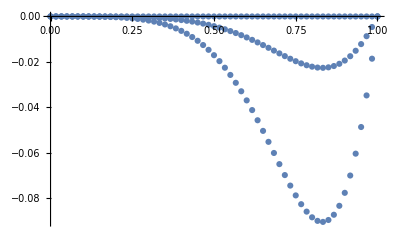

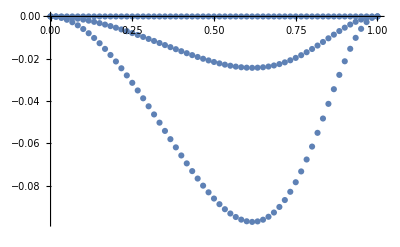

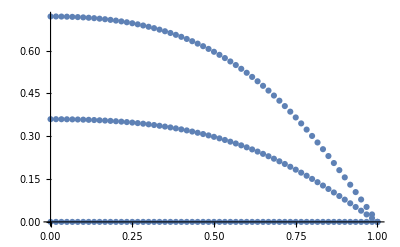

```mathematica
Show[ListPlot[Transpose[{Xrange,f2mat[[1,1;;]]}]],ListPlot[Transpose[{Xrange,f2mat[[16,1;;]]}]],ListPlot[Transpose[{Xrange,f2mat[[31,1;;]]}]],PlotRange->All]

Show[ListPlot[Transpose[{Xrange,m2mat[[1,1;;]]}]],ListPlot[Transpose[{Xrange,m2mat[[16,1;;]]}]],ListPlot[Transpose[{Xrange,m2mat[[31,1;;]]}]],PlotRange->All]

Show[ListPlot[Transpose[{Xrange,ψ1mat[[1,1;;]]}]],ListPlot[Transpose[{Xrange,ψ1mat[[16,1;;]]}]],ListPlot[Transpose[{Xrange,ψ1mat[[31,1;;]]}]],PlotRange->All]
```

## ζ^2 Fitting

### f ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{51}

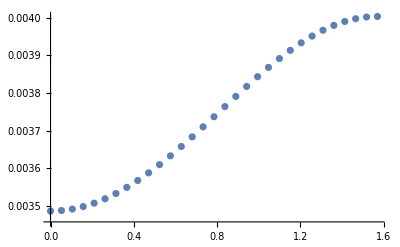

{0,2,4,6,8,10,12,14}

0.997464432234489

0.999999382359814

0.999999999808622

0.999999999948006

0.999999999947949

0.999999999946366

0.999999999947168

0.999999999945722

```mathematica
maxfpos=Ordering[Abs[u0zeta2[[Length[Yrange],1;;]]],-1]
maxfYXdata=Transpose[{Ymat[[1;;,maxfpos]]//Flatten,-u0zeta2[[1;;,maxfpos]]//Flatten}];
ListPlot[maxfYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u0maxXFitFunc={};
u0maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u0maxXFitFunc=Join[u0maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u0maxXcoeffFitFunc=Join[u0maxXcoeffFitFunc,{ctemp}],{i,yN}]

u0maxXFit=Table[0,{i,Length[u0maxXFitFunc]}];
Do[u0maxXFit[[i]]=NonlinearModelFit[maxfYXdata,u0maxXFitFunc[[i]],u0maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u0maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u0maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=6, with R^2=0.999999999948006

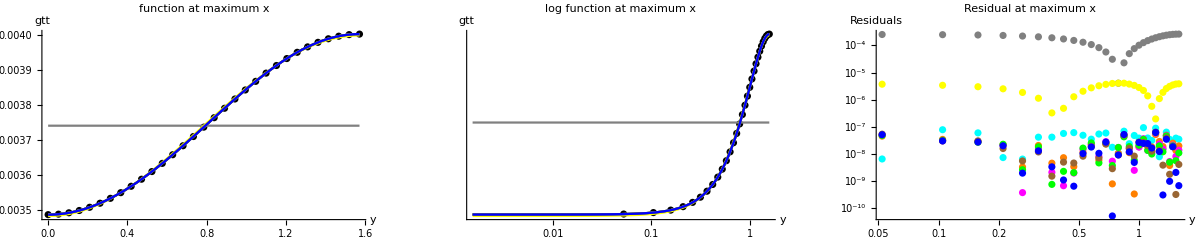

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxfXPlot=Table[0,{i,Length[u0maxXFit]+1}];
maxfXPlot[[1]]=ListPlot[maxfYXdata,PlotStyle->Black];
Do[maxfXPlot[[i+1]]=Plot[Normal[u0maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u0maxXFit]}]

maxfXLogPlot=Table[0,{i,Length[u0maxXFit]+1}];
maxfXLogPlot[[1]]=ListLogLogPlot[maxfYXdata,PlotStyle->Black];
Do[maxfXLogPlot[[i+1]]=LogLogPlot[Normal[u0maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u0maxXFit]}]

maxfXRes=Table[0,{i,Length[u0maxXFit]}];
Do[maxfXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxfpos]]//Flatten,Abs[u0maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u0maxXFit]}]


Show[GraphicsGrid[{{Show[maxfXPlot,AxesLabel->{y,gtt},PlotLabel->"function at maximum x",PlotRange->All], Show[maxfXLogPlot,AxesLabel->{y,gtt},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxfXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The magenta residuals on the right above plot correspond to r=4 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: P_6 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04 + LegendreP[6,Cos[y]] aj06)";
coeffn="{aj00,aj02,aj04,aj06}";
Xnstr="x^2 (-1+x) x^j";
Ftemp=0;
ctemp = {};
u0XFitFunc={};
u0XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u0XFitFunc=Join[u0XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u0XcoeffFitFunc=Join[u0XcoeffFitFunc,{ctemp}],{i,xN}]

u0XFit=Table[0,{i,Length[u0XFitFunc]}];
Do[u0XFit[[i]]=NonlinearModelFit[u0zeta2pts,u0XFitFunc[[i]],u0XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u0XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u0XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.6874060889359319

0.95112829806314

0.99672812114457

0.999909946061465

0.999931863173206

0.999979576723333

0.9999976942973

0.999999722056819

0.999999826949592

0.999999932581367

0.999999985521627

0.999999997910008

0.999999999318861

0.999999999341568

Here n=12

{1,16,31}

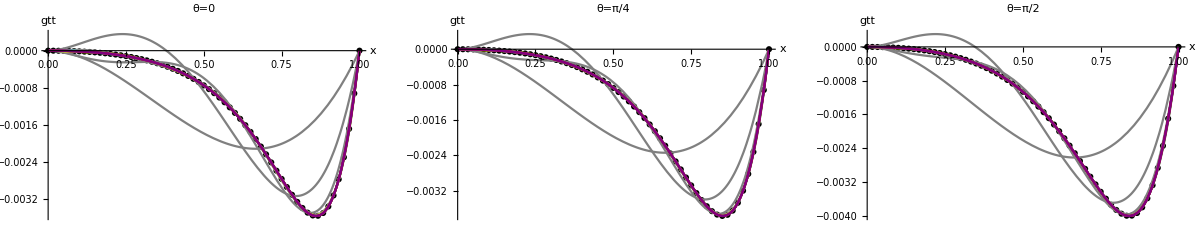

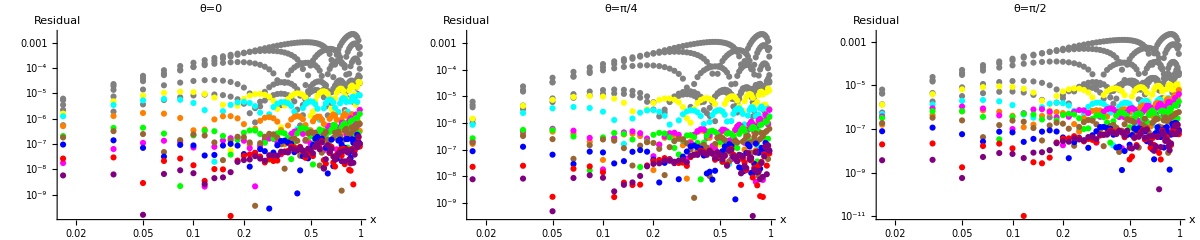

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u0XPlotY=Table[0,{i,Length[u0XFit]+1},{j,Length[Yplot]}];
Do[u0XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u0zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u0XPlotY[[i+1,j]]=Plot[u0XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u0XFit]}]
Show[GraphicsGrid[{{Show[u0XPlotY[[1;;,1]],AxesLabel->{x,gtt},PlotLabel->"θ=0",PlotRange->All],Show[u0XPlotY[[1;;,2]],AxesLabel->{x,gtt},PlotLabel->"θ=π/4",PlotRange->All],Show[u0XPlotY[[1;;,3]],AxesLabel->{x,gtt},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u0XFitRes=Table[0,{i,Length[u0XFit]}];
Do[u0XFitRes[[i]]=Partition[u0XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u0XFit]}]
u0XResY=Table[0,{i,Length[u0XFit]},{j,Length[Yplot]}];

Do[Do[u0XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u0XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u0XFit]}]
Show[GraphicsGrid[{{Show[u0XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u0XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u0XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=12 is the red residual

#### y^n Order Determination (global x-fit): Order: x^12

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="x^2(-1+x)(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j + x^9 a09j + x^10 a10j + x^11 a11j + x^12 a12j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j,a09j,a10j,a11j,a12j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u0YFitFunc={};
u0YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u0YFitFunc=Join[u0YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u0YcoeffFitFunc=Join[u0YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u0YFit=Table[0,{i,Length[u0YFitFunc]}];
Do[u0YFit[[i]]=NonlinearModelFit[u0zeta2pts,u0YFitFunc[[i]],u0YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u0YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u0YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.995363310853742

0.999985994154238

0.999999946429813

0.999999999318861

0.999999999525148

0.999999999522966

0.999999999519592

This is just verification, we determined r=6 was the saturation point only from a fit at the location where u_0 was maximum. So in that case we had a 1-dimensional fit to make. In this case, we find the value for a global fit on the x-dimension. We recover that the saturation residual is again n=6

{1,16,31}

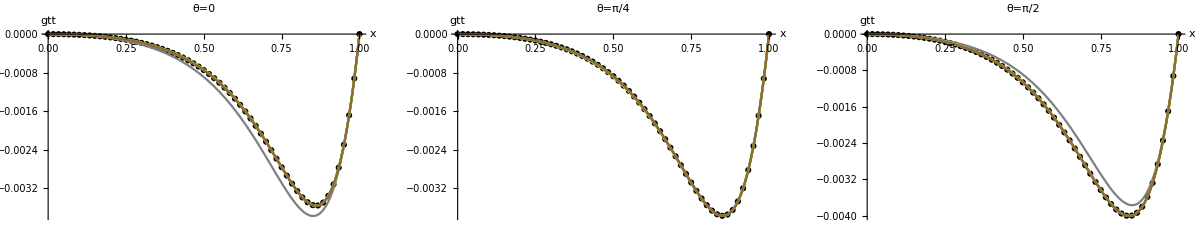

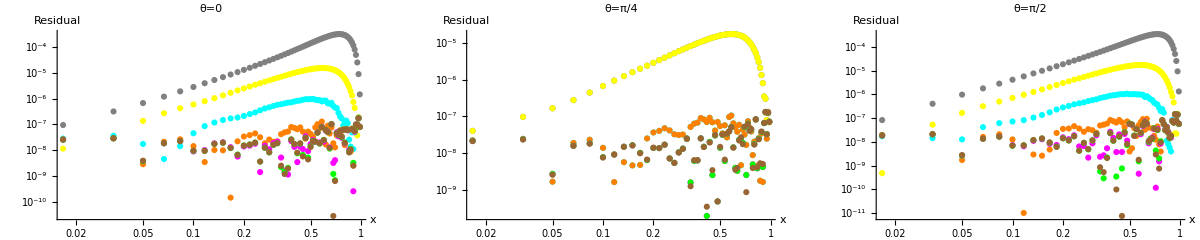

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u0YPlotY=Table[0,{i,Length[u0YFit]+1},{j,Length[Yplot]}];
Do[u0YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u0zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u0YPlotY[[i+1,j]]=Plot[u0YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u0YFit]}]
Show[GraphicsGrid[{{Show[u0YPlotY[[1;;,1]],AxesLabel->{x,gtt},PlotLabel->"θ=0",PlotRange->All],Show[u0YPlotY[[1;;,2]],AxesLabel->{x,gtt},PlotLabel->"θ=π/4",PlotRange->All],Show[u0YPlotY[[1;;,3]],AxesLabel->{x,gtt},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u0YFitRes=Table[0,{i,Length[u0YFit]}];
Do[u0YFitRes[[i]]=Partition[u0YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u0YFit]}]
u0YResY=Table[0,{i,Length[u0YFit]},{j,Length[Yplot]}];
Do[Do[u0YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u0YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u0YFit]}]

Show[GraphicsGrid[{{Show[u0YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u0YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u0YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

As explained above, n=6 is the orange residual

#### Best Fit Calculation: Order: P_6(Cos(θ)), x^12, u0YFitFunc[[4]]

```mathematica
u0FitFunc=u0YFitFunc[[4]]
u0coeffFitFunc=u0YcoeffFitFunc[[4]];
fullu0fit=NonlinearModelFit[u0zeta2pts,u0FitFunc,u0coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu0fit];
fullu0fit["BestFitParameters"]
NumberForm[fullu0fit["AdjustedRSquared"],16]
fullu0fit["ParameterTable"];
fullu0fit["ANOVATable"]
```

(-1+x) x^2 (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8+a0900 x^9+a1000 x^10+a1100 x^11+a1200 x^12)+1/2 (-1+x) x^2 (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8+a0902 x^9+a1002 x^10+a1102 x^11+a1202 x^12) (-1+3 Cos[y]^2)+1/8 (-1+x) x^2 (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8+a0904 x^9+a1004 x^10+a1104 x^11+a1204 x^12) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x) x^2 (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8+a0906 x^9+a1006 x^10+a1106 x^11+a1206 x^12) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)

{a0000→0.00192074,a0100→-0.00699936,a0200→0.222238,a0300→-2.43508,a0400→17.0928,a0500→-78.8656,a0600→249.522,a0700→-549.395,a0800→841.615,a0900→-879.628,a1000→598.17,a1100→-238.469,a1200→42.2355,a0002→-0.000410087,a0102→-0.00342314,a0202→0.0502261,a0302→-0.581984,a0402→4.00264,a0502→-18.2084,a0602→56.4184,a0702→-121.016,a0802→179.314,a0902→-179.616,a1002→115.617,a1102→-42.8566,a1202→6.88074,a0004→0.000125505,a0104→-0.000151604,a0204→0.0073039,a0304→-0.0717064,a0404→0.44672,a0504→-1.84563,a0604→5.22227,a0704→-10.2927,a0804→14.0973,a0904→-13.1427,a1004→7.9385,a1104→-2.78991,a1204→0.430614,a0006→-0.000022434,a0106→0.000440395,a0206→-0.00927602,a0306→0.099498,a0406→-0.654855,a0506→2.82505,a0606→-8.27782,a0706→16.7569,a0806→-23.4395,a0906→22.2415,a1006→-13.6688,a1106→4.9095,a1206→-0.782661}

0.999999999318861

| DF | SS | MS
Model | 52 | 6.53974×10^7 | 1.25764×10^6
Error | 1839 | 0.0433198 | 0.0000235562
Uncorrected Total | 1891 | 6.53974×10^7 | 
Corrected Total | 1890 | 3.3006×10^7 |

#### Best Fit Comparison

```mathematica
u0fitres=Partition[fullu0fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u0Plot=Table[0,5,{i,Length[Yplot]}];

Do[u0Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u0zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u0Plot[[2,j]]=Plot[fullu0fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u0Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u0zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u0Plot[[4,j]]=LogLogPlot[Abs[fullu0fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u0Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u0fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

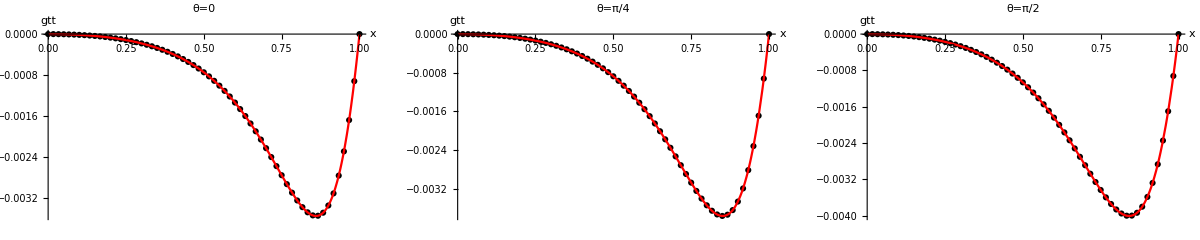

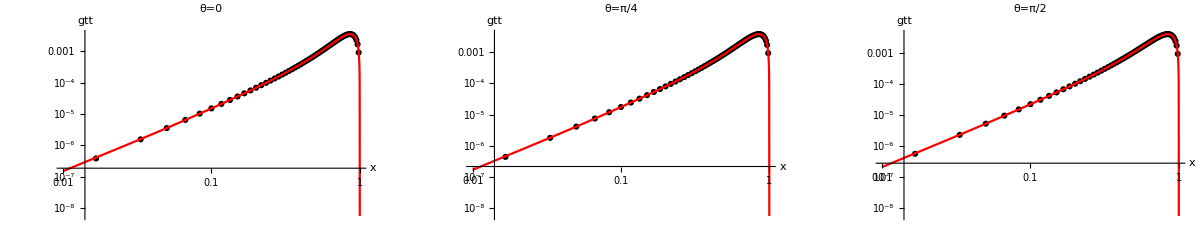

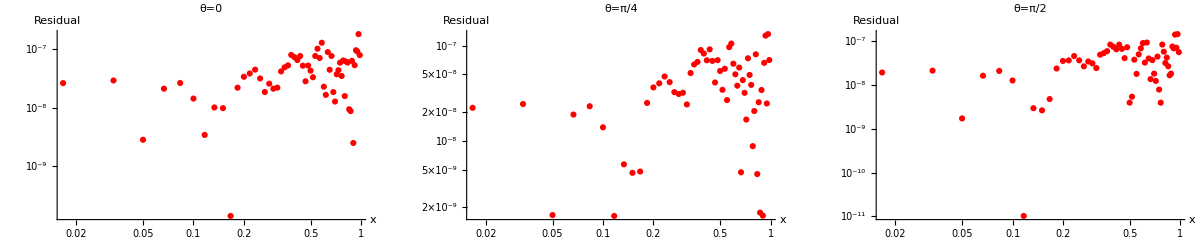

```mathematica
Show[GraphicsGrid[{{Show[u0Plot[[1;;2,1]],AxesLabel->{x,gtt},PlotLabel->"θ=0",PlotRange->All],Show[u0Plot[[1;;2,2]],AxesLabel->{x,gtt},PlotLabel->"θ=π/4",PlotRange->All],Show[u0Plot[[1;;2,3]],AxesLabel->{x,gtt},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u0Plot[[3;;4,1]],AxesLabel->{x,gtt},PlotLabel->"θ=0",PlotRange->All],Show[u0Plot[[3;;4,2]],AxesLabel->{x,gtt},PlotLabel->"θ=π/4",PlotRange->All],Show[u0Plot[[3;;4,3]],AxesLabel->{x,gtt},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u0Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u0Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u0Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

### m ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{38}

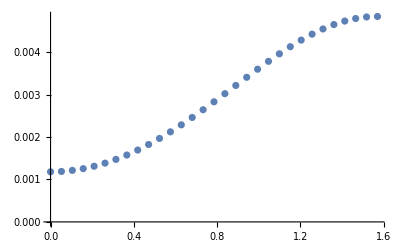

{0,2,4,6,8,10,12,14}

0.826494411105007

0.999560366992046

0.999998855542263

0.999999997298991

0.999999999778988

0.999999999770147

0.999999999760812

0.999999999753195

```mathematica
maxmpos=Ordering[Abs[u1zeta2[[Length[Yrange],1;;]]],-1]
maxmYXdata=Transpose[{Ymat[[1;;,maxmpos]]//Flatten,-u1zeta2[[1;;,maxmpos]]//Flatten}];
ListPlot[maxmYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u1maxXFitFunc={};
u1maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u1maxXFitFunc=Join[u1maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u1maxXcoeffFitFunc=Join[u1maxXcoeffFitFunc,{ctemp}],{i,yN}]

u1maxXFit=Table[0,{i,Length[u1maxXFitFunc]}];
Do[u1maxXFit[[i]]=NonlinearModelFit[maxmYXdata,u1maxXFitFunc[[i]],u1maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u1maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u1maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=8, with R^2=0.999999999778988

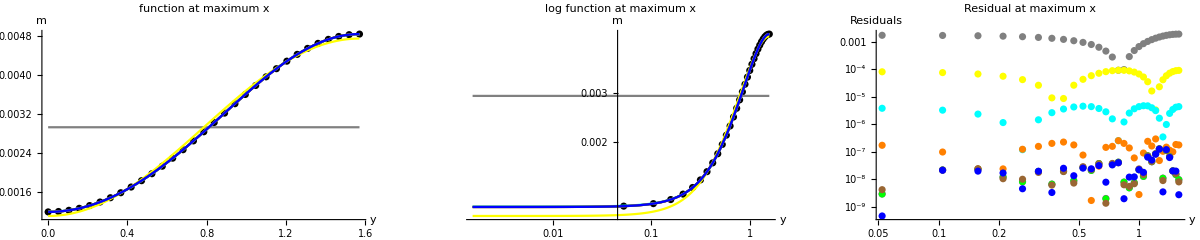

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxmXPlot=Table[0,{i,Length[u1maxXFit]+1}];
maxmXPlot[[1]]=ListPlot[maxmYXdata,PlotStyle->Black];
Do[maxmXPlot[[i+1]]=Plot[Normal[u1maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u1maxXFit]}]

maxmXLogPlot=Table[0,{i,Length[u1maxXFit]+1}];
maxmXLogPlot[[1]]=ListLogLogPlot[maxmYXdata,PlotStyle->Black];
Do[maxmXLogPlot[[i+1]]=LogLogPlot[Normal[u1maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u1maxXFit]}]

maxmXRes=Table[0,{i,Length[u1maxXFit]}];
Do[maxmXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxmpos]]//Flatten,Abs[u1maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u1maxXFit]}]


Show[GraphicsGrid[{{Show[maxmXPlot,AxesLabel->{y,m},PlotLabel->"function at maximum x",PlotRange->All], Show[maxmXLogPlot,AxesLabel->{y,m},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxmXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The magenta residuals on the right above plot correspond to r=8 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: P_8 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04 + LegendreP[6,Cos[y]] aj06 + LegendreP[8,Cos[y]] aj08)";
coeffn="{aj00,aj02,aj04,aj06,aj08}";
Xnstr="x^2 (-1+x)^2 x^j";
Ftemp=0;
ctemp = {};
u1XFitFunc={};
u1XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u1XFitFunc=Join[u1XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u1XcoeffFitFunc=Join[u1XcoeffFitFunc,{ctemp}],{i,xN}]

u1XFit=Table[0,{i,Length[u1XFitFunc]}];
Do[u1XFit[[i]]=NonlinearModelFit[u1zeta2pts,u1XFitFunc[[i]],u1XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u1XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u1XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.902946953626142

0.991951604899623

0.999714223287411

0.999967655019136

0.99997639718729

0.999993049839034

0.999998812659817

0.99999987850666

0.999999993847351

0.999999999330946

0.999999999340986

0.999999999430404

0.999999999443953

0.999999999448288

Here n=9

{1,16,31}

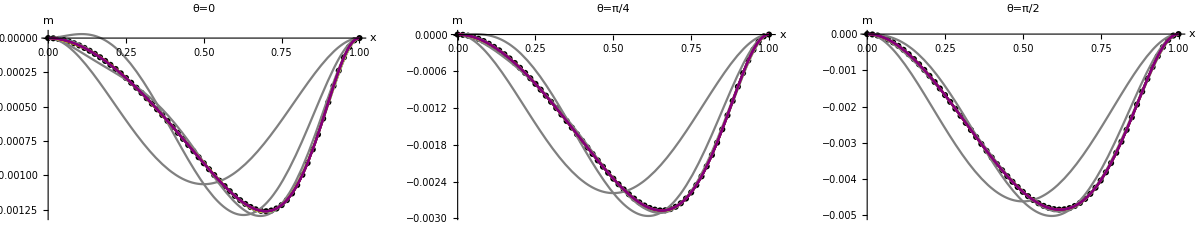

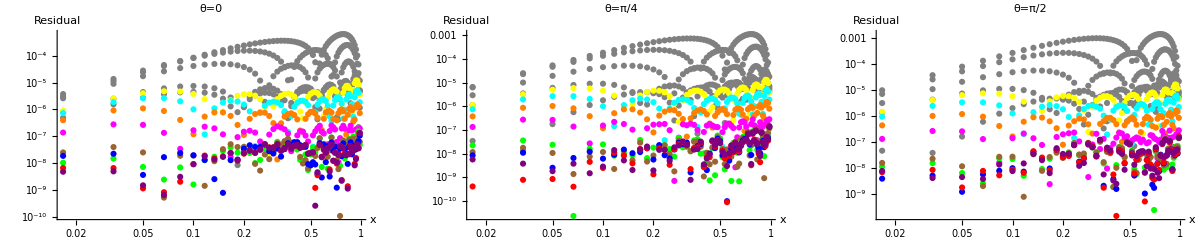

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u1XPlotY=Table[0,{i,Length[u1XFit]+1},{j,Length[Yplot]}];
Do[u1XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u1zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u1XPlotY[[i+1,j]]=Plot[u1XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u1XFit]}]
Show[GraphicsGrid[{{Show[u1XPlotY[[1;;,1]],AxesLabel->{x,m},PlotLabel->"θ=0",PlotRange->All],Show[u1XPlotY[[1;;,2]],AxesLabel->{x,m},PlotLabel->"θ=π/4",PlotRange->All],Show[u1XPlotY[[1;;,3]],AxesLabel->{x,m},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u1XFitRes=Table[0,{i,Length[u1XFit]}];
Do[u1XFitRes[[i]]=Partition[u1XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u1XFit]}]
u1XResY=Table[0,{i,Length[u1XFit]},{j,Length[Yplot]}];

Do[Do[u1XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u1XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u1XFit]}]
Show[GraphicsGrid[{{Show[u1XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u1XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u1XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=9 is the green residual

#### y^n Order Determination (global x-fit): Order: x^9

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="x^2(-1+x)^2(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j + x^9 a09j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j,a09j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u1YFitFunc={};
u1YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u1YFitFunc=Join[u1YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u1YcoeffFitFunc=Join[u1YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u1YFit=Table[0,{i,Length[u1YFitFunc]}];
Do[u1YFit[[i]]=NonlinearModelFit[u1zeta2pts,u1YFitFunc[[i]],u1YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u1YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u1YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.828644723383052

0.999090550947227

0.999995766806196

0.999999981349263

0.999999999330946

0.999999999412098

0.999999999410314

This is just verification, we determined y^8 was the saturation point only from a fit at the location where u_0 was maximum. So in that case we had a 1-dimensional fit to make. In this case, we find the y^n value for a global fit on the x-dimension. We recover that the saturation residual is again n=8

{1,16,31}

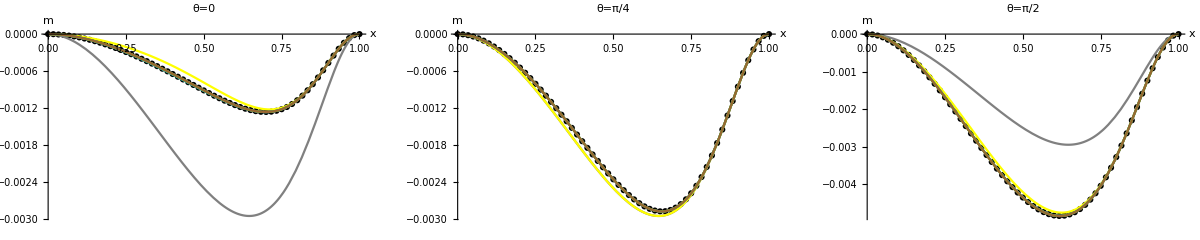

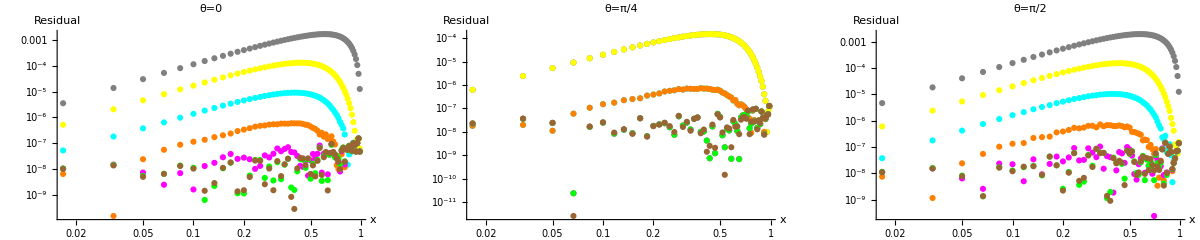

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u1YPlotY=Table[0,{i,Length[u1YFit]+1},{j,Length[Yplot]}];
Do[u1YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u1zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u1YPlotY[[i+1,j]]=Plot[u1YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u1YFit]}]
Show[GraphicsGrid[{{Show[u1YPlotY[[1;;,1]],AxesLabel->{x,m},PlotLabel->"θ=0",PlotRange->All],Show[u1YPlotY[[1;;,2]],AxesLabel->{x,m},PlotLabel->"θ=π/4",PlotRange->All],Show[u1YPlotY[[1;;,3]],AxesLabel->{x,m},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u1YFitRes=Table[0,{i,Length[u1YFit]}];
Do[u1YFitRes[[i]]=Partition[u1YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u1YFit]}]
u1YResY=Table[0,{i,Length[u1YFit]},{j,Length[Yplot]}];
Do[Do[u1YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u1YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u1YFit]}]

Show[GraphicsGrid[{{Show[u1YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u1YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u1YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

As explained above, n=8 is the magenta residual

#### Best Fit Calculation: Order: P_8, x^9, u0YFitFunc[[5]]

```mathematica
u1FitFunc=u1YFitFunc[[5]]
u1coeffFitFunc=u1YcoeffFitFunc[[5]];
fullu1fit=NonlinearModelFit[u1zeta2pts,u1FitFunc,u1coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu1fit];
fullu1fit["BestFitParameters"]
NumberForm[fullu1fit["AdjustedRSquared"],16]
fullu1fit["ParameterTable"];
fullu1fit["ANOVATable"]
```

(-1+x)^2 x^2 (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8+a0900 x^9)+1/2 (-1+x)^2 x^2 (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8+a0902 x^9) (-1+3 Cos[y]^2)+1/8 (-1+x)^2 x^2 (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8+a0904 x^9) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x)^2 x^2 (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8+a0906 x^9) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)+1/128 (-1+x)^2 x^2 (a0008+a0108 x+a0208 x^2+a0308 x^3+a0408 x^4+a0508 x^5+a0608 x^6+a0708 x^7+a0808 x^8+a0908 x^9) (35-1260 Cos[y]^2+6930 Cos[y]^4-12012 Cos[y]^6+6435 Cos[y]^8)

{a0000→-0.0237399,a0100→-0.0185324,a0200→-0.105798,a0300→0.618027,a0400→-3.18734,a0500→9.59926,a0600→-18.5792,a0700→22.0823,a0800→-14.8822,a0900→4.37689,a0002→0.0214391,a0102→0.0222073,a0202→0.00453542,a0302→0.103203,a0402→-0.41899,a0502→1.18179,a0602→-1.95355,a0702→1.84455,a0802→-0.829193,a0902→0.08561,a0004→-0.00406999,a0104→-0.00696562,a0204→0.0400924,a0304→-0.264758,a0404→1.14006,a0504→-2.86526,a0604→4.46302,a0704→-4.08713,a0804→1.93934,a0904→-0.354087,a0006→0.000409539,a0106→0.000672215,a0206→-0.00384938,a0306→0.0238379,a0406→-0.112017,a0506→0.309759,a0606→-0.548627,a0706→0.597233,a0806→-0.3524,a0906→0.0849664,a0008→-0.0000441697,a0108→0.000271125,a0208→-0.00434781,a0308→0.0324583,a0408→-0.135987,a0508→0.347201,a0608→-0.543763,a0708→0.507702,a0808→-0.259166,a0908→0.0556765}

0.999999999330946

| DF | SS | MS
Model | 50 | 7.52232×10^7 | 1.50446×10^6
Error | 1841 | 0.0489976 | 0.0000266147
Uncorrected Total | 1891 | 7.52232×10^7 | 
Corrected Total | 1890 | 3.33358×10^7 |

#### Best Fit Comparison

```mathematica
u1fitres=Partition[fullu1fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u1Plot=Table[0,5,{i,Length[Yplot]}];

Do[u1Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u1zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u1Plot[[2,j]]=Plot[fullu1fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u1Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u1zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u1Plot[[4,j]]=LogLogPlot[Abs[fullu1fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u1Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u1fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

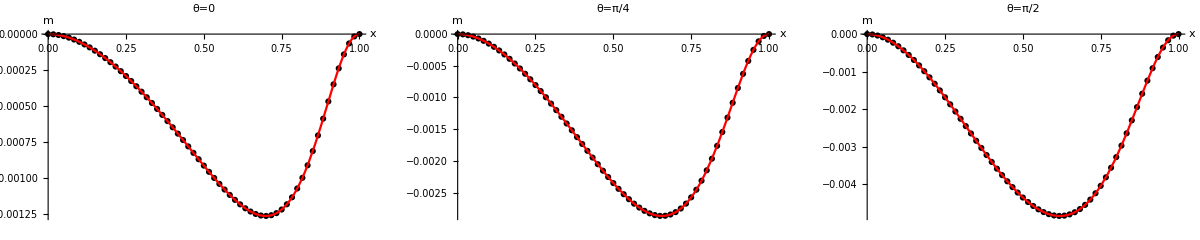

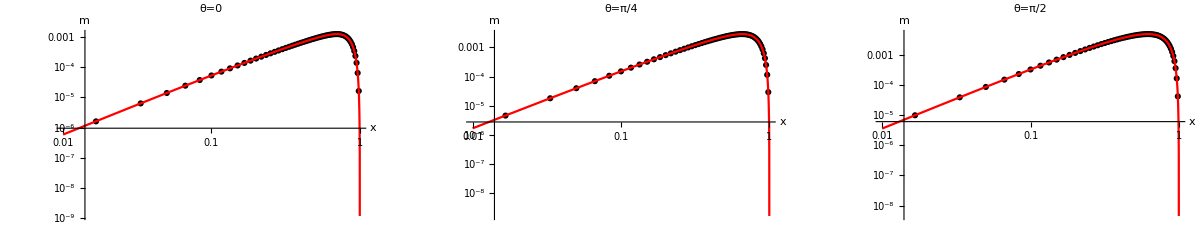

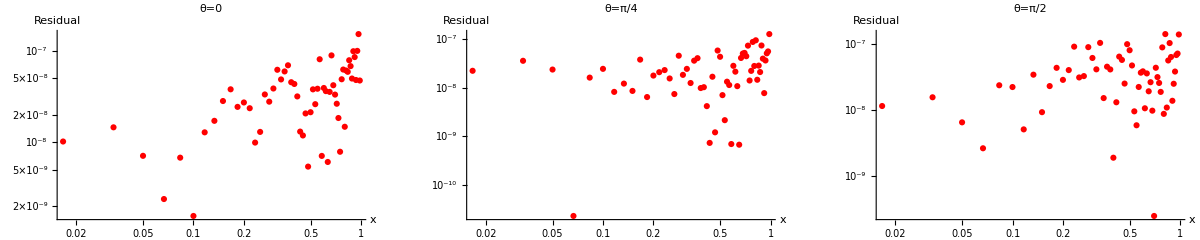

```mathematica
Show[GraphicsGrid[{{Show[u1Plot[[1;;2,1]],AxesLabel->{x,m},PlotLabel->"θ=0",PlotRange->All],Show[u1Plot[[1;;2,2]],AxesLabel->{x,m},PlotLabel->"θ=π/4",PlotRange->All],Show[u1Plot[[1;;2,3]],AxesLabel->{x,m},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u1Plot[[3;;4,1]],AxesLabel->{x,m},PlotLabel->"θ=0",PlotRange->All],Show[u1Plot[[3;;4,2]],AxesLabel->{x,m},PlotLabel->"θ=π/4",PlotRange->All],Show[u1Plot[[3;;4,3]],AxesLabel->{x,m},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u1Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u1Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u1Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

### l ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{44}

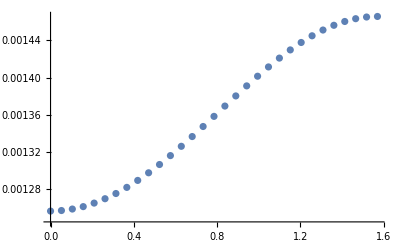

{0,2,4,6,8,10,12,14}

0.996841701697678

0.999999424839002

0.999999995585565

0.999999999444172

0.999999999422814

0.999999999400021

0.999999999378917

0.999999999353296

```mathematica
maxlpos=Ordering[Abs[u2zeta2[[Length[Yrange],1;;]]],-1]
maxlYXdata=Transpose[{Ymat[[1;;,maxlpos]]//Flatten,-u2zeta2[[1;;,maxlpos]]//Flatten}];
ListPlot[maxlYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u2maxXFitFunc={};
u2maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u2maxXFitFunc=Join[u2maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u2maxXcoeffFitFunc=Join[u2maxXcoeffFitFunc,{ctemp}],{i,yN}]

u2maxXFit=Table[0,{i,Length[u2maxXFitFunc]}];
Do[u2maxXFit[[i]]=NonlinearModelFit[maxlYXdata,u2maxXFitFunc[[i]],u2maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u2maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u2maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=6, with R^2=0.999999999444172

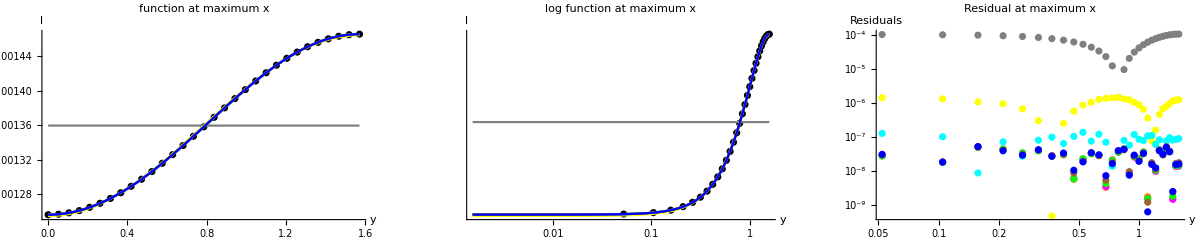

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxlXPlot=Table[0,{i,Length[u2maxXFit]+1}];
maxlXPlot[[1]]=ListPlot[maxlYXdata,PlotStyle->Black];
Do[maxlXPlot[[i+1]]=Plot[Normal[u2maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u2maxXFit]}]

maxlXLogPlot=Table[0,{i,Length[u2maxXFit]+1}];
maxlXLogPlot[[1]]=ListLogLogPlot[maxlYXdata,PlotStyle->Black];
Do[maxlXLogPlot[[i+1]]=LogLogPlot[Normal[u2maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u2maxXFit]}]

maxlXRes=Table[0,{i,Length[u2maxXFit]}];
Do[maxlXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxlpos]]//Flatten,Abs[u2maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u2maxXFit]}]


Show[GraphicsGrid[{{Show[maxlXPlot,AxesLabel->{y,l},PlotLabel->"function at maximum x",PlotRange->All], Show[maxlXLogPlot,AxesLabel->{y,l},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxlXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The brown residuals on the right above plot correspond to r=6 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: y^6 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04 + LegendreP[6,Cos[y]] aj06)";
coeffn="{aj00,aj02,aj04,aj06}";
Xnstr="x^2 (-1+x)^2 x^j";
Ftemp=0;
ctemp = {};
u2XFitFunc={};
u2XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u2XFitFunc=Join[u2XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u2XcoeffFitFunc=Join[u2XcoeffFitFunc,{ctemp}],{i,xN}]

u2XFit=Table[0,{i,Length[u2XFitFunc]}];
Do[u2XFit[[i]]=NonlinearModelFit[u2zeta2pts,u2XFitFunc[[i]],u2XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u2XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u2XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.7401918542487005

0.968125609304679

0.998739882283629

0.99982715340731

0.999907399212602

0.999976683512281

0.999996522197873

0.999999687824783

0.999999957847832

0.999999964590477

0.999999967676475

0.999999969865569

0.999999970499818

0.999999970573145

Here n=8

{1,16,31}

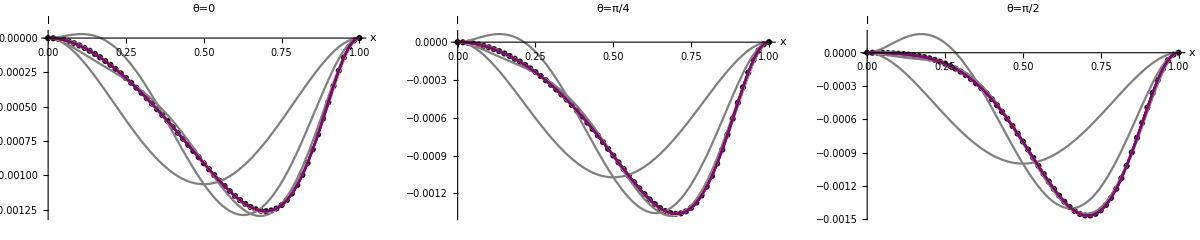

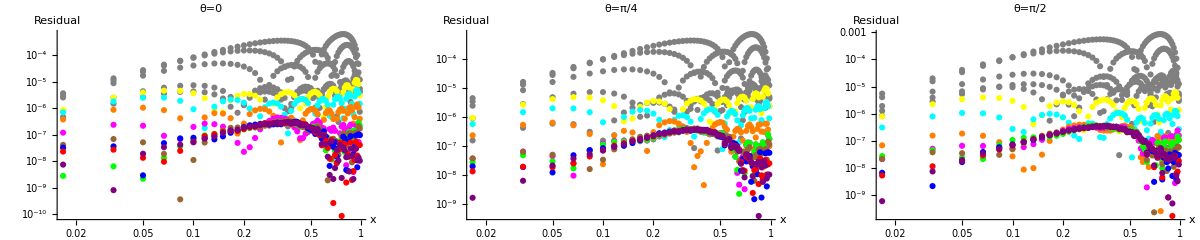

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u2XPlotY=Table[0,{i,Length[u2XFit]+1},{j,Length[Yplot]}];
Do[u2XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u2zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u2XPlotY[[i+1,j]]=Plot[u2XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u2XFit]}]
Show[GraphicsGrid[{{Show[u2XPlotY[[1;;,1]],AxesLabel->{x,l},PlotLabel->"θ=0",PlotRange->All],Show[u2XPlotY[[1;;,2]],AxesLabel->{x,l},PlotLabel->"θ=π/4",PlotRange->All],Show[u2XPlotY[[1;;,3]],AxesLabel->{x,l},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u2XFitRes=Table[0,{i,Length[u2XFit]}];
Do[u2XFitRes[[i]]=Partition[u2XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u2XFit]}]
u2XResY=Table[0,{i,Length[u2XFit]},{j,Length[Yplot]}];

Do[Do[u2XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u2XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u2XFit]}]
Show[GraphicsGrid[{{Show[u2XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u2XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u2XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=8 is the magenta residual

#### y^n Order Determination (global x-fit): Order: x^8

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="x^2(-1+x)^2(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u2YFitFunc={};
u2YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u2YFitFunc=Join[u2YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u2YcoeffFitFunc=Join[u2YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u2YFit=Table[0,{i,Length[u2YFitFunc]}];
Do[u2YFit[[i]]=NonlinearModelFit[u2zeta2pts,u2YFitFunc[[i]],u2YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u2YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u2YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.99540222145732

0.999789944100091

0.999996765771499

0.999999957847832

0.999999986117368

0.999999986268356

0.999999986202865

n=6

{1,16,31}

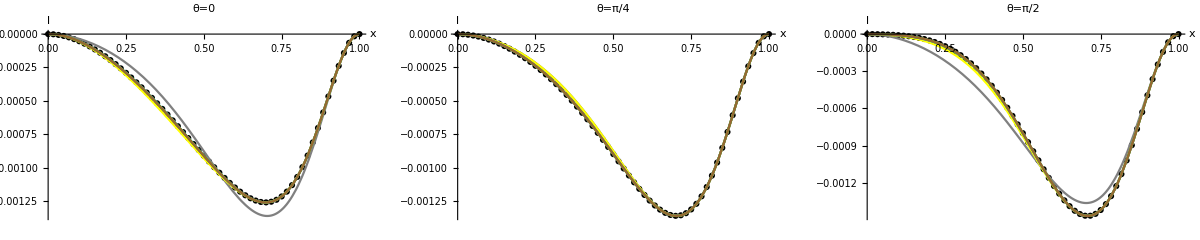

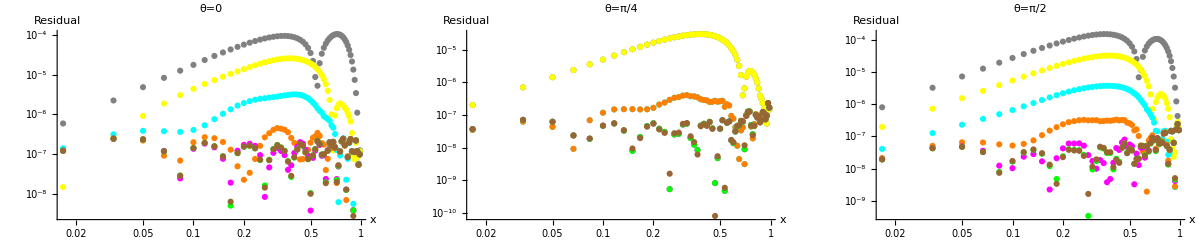

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u2YPlotY=Table[0,{i,Length[u2YFit]+1},{j,Length[Yplot]}];
Do[u2YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u2zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u2YPlotY[[i+1,j]]=Plot[u2YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u2YFit]}]
Show[GraphicsGrid[{{Show[u2YPlotY[[1;;,1]],AxesLabel->{x,l},PlotLabel->"θ=0",PlotRange->All],Show[u2YPlotY[[1;;,2]],AxesLabel->{x,l},PlotLabel->"θ=π/4",PlotRange->All],Show[u2YPlotY[[1;;,3]],AxesLabel->{x,l},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u2YFitRes=Table[0,{i,Length[u2YFit]}];
Do[u2YFitRes[[i]]=Partition[u2YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u2YFit]}]
u2YResY=Table[0,{i,Length[u2YFit]},{j,Length[Yplot]}];
Do[Do[u2YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u2YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u2YFit]}]

Show[GraphicsGrid[{{Show[u2YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u2YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u2YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

n=6 is the orange residual which isn’t the saturation for θ=0,π/2, so n=8 is the magenta residual

#### Best Fit Calculation: Order: P_8, x^8, u2YFitFunc[[5]]

```mathematica
u2FitFunc=u2YFitFunc[[5]]
u2coeffFitFunc=u2YcoeffFitFunc[[5]];
fullu2fit=NonlinearModelFit[u2zeta2pts,u2FitFunc,u2coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu2fit];
fullu2fit["BestFitParameters"]
NumberForm[fullu2fit["AdjustedRSquared"],16]
fullu2fit["ParameterTable"];
fullu2fit["ANOVATable"]
```

(-1+x)^2 x^2 (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8)+1/2 (-1+x)^2 x^2 (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8) (-1+3 Cos[y]^2)+1/8 (-1+x)^2 x^2 (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x)^2 x^2 (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)+1/128 (-1+x)^2 x^2 (a0008+a0108 x+a0208 x^2+a0308 x^3+a0408 x^4+a0508 x^5+a0608 x^6+a0708 x^7+a0808 x^8) (35-1260 Cos[y]^2+6930 Cos[y]^4-12012 Cos[y]^6+6435 Cos[y]^8)

{a0000→-0.00300347,a0100→-0.00804232,a0200→0.051956,a0300→-0.480631,a0400→1.80308,a0500→-4.43508,a0600→6.32362,a0700→-5.02722,a0800→1.7153,a0002→-0.00314546,a0102→-0.0220233,a0202→0.225757,a0302→-1.3572,a0402→4.95328,a0502→-10.6422,a0602→13.5783,a0702→-9.44789,a0802→2.71531,a0004→0.00119522,a0104→-0.00155691,a0204→0.0284979,a0304→-0.17656,a0404→0.560461,a0504→-1.07779,a0604→1.17368,a0704→-0.637146,a0804→0.128973,a0006→-0.000184623,a0106→0.000164718,a0206→-0.00387708,a0306→0.0272584,a0406→-0.0962599,a0506→0.209957,a0606→-0.268032,a0706→0.17882,a0806→-0.047858,a0008→0.0000167729,a0108→0.000117422,a0208→-0.00111638,a0308→0.00589835,a0408→-0.0189994,a0508→0.0345527,a0608→-0.0348358,a0708→0.0182139,a0808→-0.00384255}

0.999999986117368

| DF | SS | MS
Model | 45 | 1.12818×10^7 | 250707.
Error | 1846 | 0.152894 | 0.0000828246
Uncorrected Total | 1891 | 1.12818×10^7 | 
Corrected Total | 1890 | 4.44822×10^6 |

#### Best Fit Comparison

```mathematica
u2fitres=Partition[fullu2fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u2Plot=Table[0,5,{i,Length[Yplot]}];

Do[u2Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u2zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u2Plot[[2,j]]=Plot[fullu2fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u2Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u2zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u2Plot[[4,j]]=LogLogPlot[Abs[fullu2fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u2Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u2fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

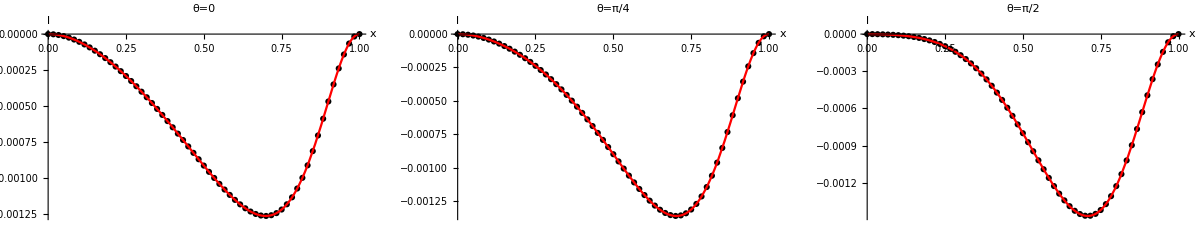

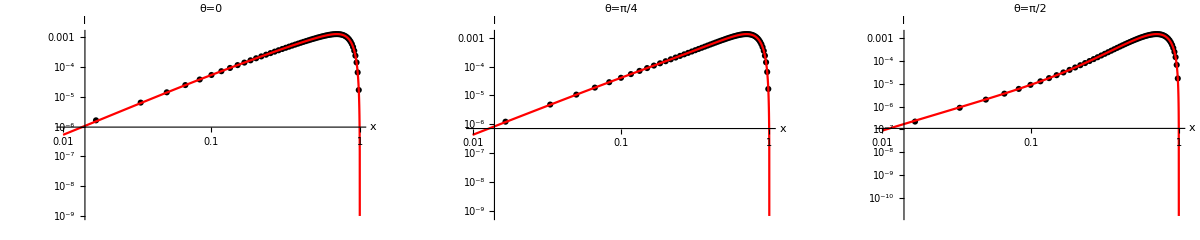

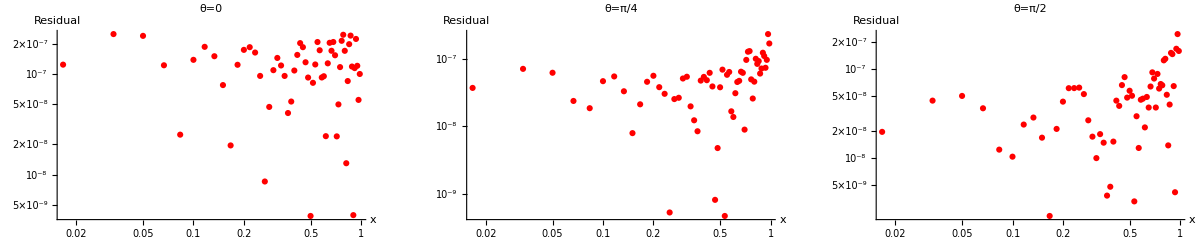

```mathematica
Show[GraphicsGrid[{{Show[u2Plot[[1;;2,1]],AxesLabel->{x,l},PlotLabel->"θ=0",PlotRange->All],Show[u2Plot[[1;;2,2]],AxesLabel->{x,l},PlotLabel->"θ=π/4",PlotRange->All],Show[u2Plot[[1;;2,3]],AxesLabel->{x,l},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u2Plot[[3;;4,1]],AxesLabel->{x,l},PlotLabel->"θ=0",PlotRange->All],Show[u2Plot[[3;;4,2]],AxesLabel->{x,l},PlotLabel->"θ=π/4",PlotRange->All],Show[u2Plot[[3;;4,3]],AxesLabel->{x,l},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u2Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u2Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u2Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

### ω ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{50}

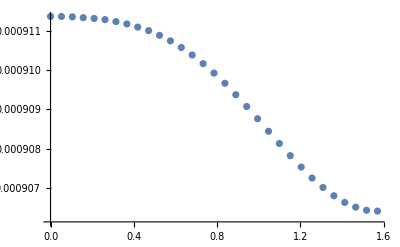

{0,2,4,6,8,10,12,14}

0.999995911125375

0.999999821062445

0.99999999986473

0.999999999992561

0.999999999992289

0.999999999991989

0.999999999991716

0.999999999991483

```mathematica
maxopos=Ordering[Abs[u3zeta2[[Length[Yrange],1;;]]],-1]
maxoYXdata=Transpose[{Ymat[[1;;,maxopos]]//Flatten,u3zeta2[[1;;,maxopos]]//Flatten}];
ListPlot[maxoYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u3maxXFitFunc={};
u3maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u3maxXFitFunc=Join[u3maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u3maxXcoeffFitFunc=Join[u3maxXcoeffFitFunc,{ctemp}],{i,yN}]

u3maxXFit=Table[0,{i,Length[u3maxXFitFunc]}];
Do[u3maxXFit[[i]]=NonlinearModelFit[maxoYXdata,u3maxXFitFunc[[i]],u3maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u3maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u3maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=6, with R^2=0.999999999992561

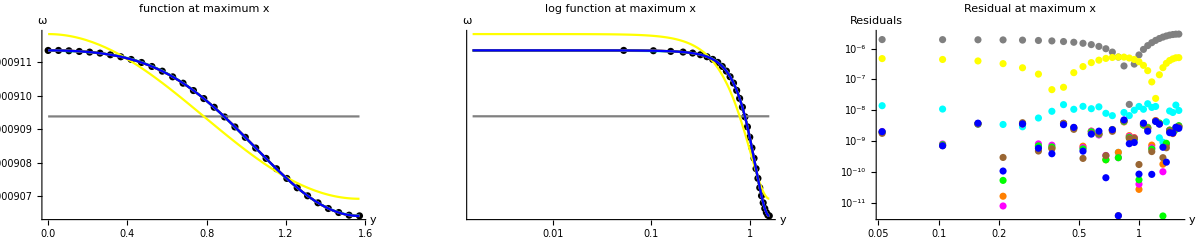

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxoXPlot=Table[0,{i,Length[u3maxXFit]+1}];
maxoXPlot[[1]]=ListPlot[maxoYXdata,PlotStyle->Black];
Do[maxoXPlot[[i+1]]=Plot[Normal[u3maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u3maxXFit]}]

maxoXLogPlot=Table[0,{i,Length[u3maxXFit]+1}];
maxoXLogPlot[[1]]=ListLogLogPlot[maxoYXdata,PlotStyle->Black];
Do[maxoXLogPlot[[i+1]]=LogLogPlot[Normal[u3maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u3maxXFit]}]

maxoXRes=Table[0,{i,Length[u3maxXFit]}];
Do[maxoXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxopos]]//Flatten,Abs[u3maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u3maxXFit]}]


Show[GraphicsGrid[{{Show[maxoXPlot,AxesLabel->{y,ω},PlotLabel->"function at maximum x",PlotRange->All], Show[maxoXLogPlot,AxesLabel->{y,ω},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxoXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The orange residuals on the right above plot correspond to r=6 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: y^6 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04 + LegendreP[6,Cos[y]] aj06)";
coeffn="{aj00,aj02,aj04,aj06}";
Xnstr="(-1+x)^2 x^j";
Ftemp=0;
ctemp = {};
u3XFitFunc={};
u3XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u3XFitFunc=Join[u3XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u3XcoeffFitFunc=Join[u3XcoeffFitFunc,{ctemp}],{i,xN}]

u3XFit=Table[0,{i,Length[u3XFitFunc]}];
Do[u3XFit[[i]]=NonlinearModelFit[u3zeta2pts,u3XFitFunc[[i]],u3XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u3XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u3XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.02725885680624492

0.2401914040548025

0.5882919554767537

0.840879406044756

0.953926758593643

0.989756739875596

0.998259267173923

0.999783943181262

0.999982870400063

0.999999432480568

0.999999961281248

0.999999969359026

0.999999991810031

0.999999997944924

Here n=10

{1,16,31}

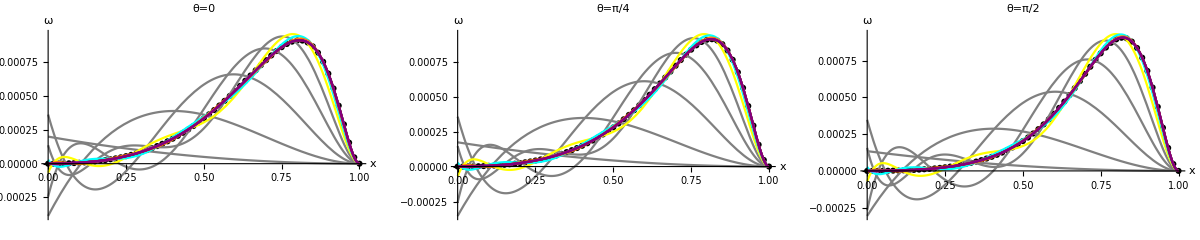

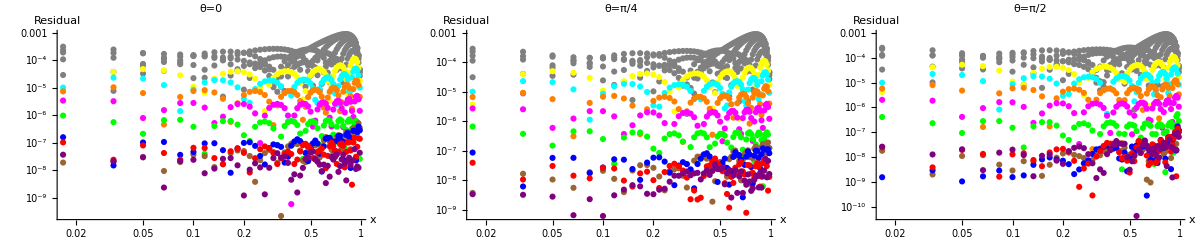

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u3XPlotY=Table[0,{i,Length[u3XFit]+1},{j,Length[Yplot]}];
Do[u3XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u3zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u3XPlotY[[i+1,j]]=Plot[u3XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u3XFit]}]
Show[GraphicsGrid[{{Show[u3XPlotY[[1;;,1]],AxesLabel->{x,ω},PlotLabel->"θ=0",PlotRange->All],Show[u3XPlotY[[1;;,2]],AxesLabel->{x,ω},PlotLabel->"θ=π/4",PlotRange->All],Show[u3XPlotY[[1;;,3]],AxesLabel->{x,ω},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u3XFitRes=Table[0,{i,Length[u3XFit]}];
Do[u3XFitRes[[i]]=Partition[u3XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u3XFit]}]
u3XResY=Table[0,{i,Length[u3XFit]},{j,Length[Yplot]}];

Do[Do[u3XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u3XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u3XFit]}]
Show[GraphicsGrid[{{Show[u3XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u3XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u3XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=10 is the brown residual

#### y^n Order Determination (global x-fit): Order: x^10

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="(-1+x)^2(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j + x^9 a09j + x^10 a10j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j,a09j,a10j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u3YFitFunc={};
u3YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u3YFitFunc=Join[u3YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u3YcoeffFitFunc=Join[u3YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u3YFit=Table[0,{i,Length[u3YFitFunc]}];
Do[u3YFit[[i]]=NonlinearModelFit[u3zeta2pts,u3YFitFunc[[i]],u3YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u3YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u3YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.996178859745286

0.999976048996252

0.999999879429044

0.999999961281248

0.99999996136847

0.999999961137037

0.999999960901448

n=6

{1,16,31}

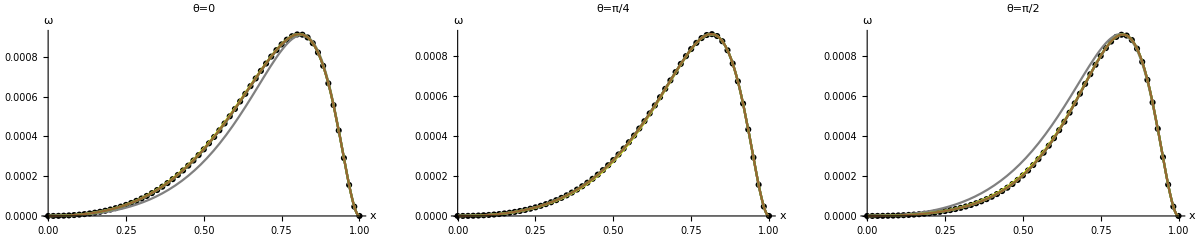

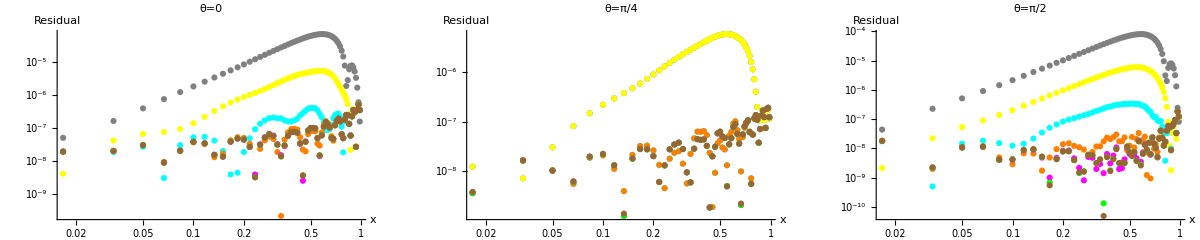

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u3YPlotY=Table[0,{i,Length[u3YFit]+1},{j,Length[Yplot]}];
Do[u3YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u3zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u3YPlotY[[i+1,j]]=Plot[u3YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u3YFit]}]
Show[GraphicsGrid[{{Show[u3YPlotY[[1;;,1]],AxesLabel->{x,ω},PlotLabel->"θ=0",PlotRange->All],Show[u3YPlotY[[1;;,2]],AxesLabel->{x,ω},PlotLabel->"θ=π/4",PlotRange->All],Show[u3YPlotY[[1;;,3]],AxesLabel->{x,ω},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u3YFitRes=Table[0,{i,Length[u3YFit]}];
Do[u3YFitRes[[i]]=Partition[u3YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u3YFit]}]
u3YResY=Table[0,{i,Length[u3YFit]},{j,Length[Yplot]}];
Do[Do[u3YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u3YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u3YFit]}]

Show[GraphicsGrid[{{Show[u3YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u3YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u3YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

n=6 is the orange residual

#### Best Fit Calculation: Order: P_6, x^10, u3YFitFunc[[4]]

```mathematica
u3FitFunc=u3YFitFunc[[4]]
u3coeffFitFunc=u3YcoeffFitFunc[[4]];
fullu3fit=NonlinearModelFit[u3zeta2pts,u3FitFunc,u3coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu3fit];
fullu3fit["BestFitParameters"]
NumberForm[fullu3fit["AdjustedRSquared"],16]
fullu3fit["ParameterTable"];
fullu3fit["ANOVATable"]
```

(-1+x)^2 (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8+a0900 x^9+a1000 x^10)+1/2 (-1+x)^2 (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8+a0902 x^9+a1002 x^10) (-1+3 Cos[y]^2)+1/8 (-1+x)^2 (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8+a0904 x^9+a1004 x^10) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x)^2 (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8+a0906 x^9+a1006 x^10) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)

{a0000→-9.1781×10^-10,a0100→-2.7153×10^-6,a0200→0.000569712,a0300→-0.0045254,a0400→0.0774893,a0500→-0.507938,a0600→2.11964,a0700→-5.28002,a0800→8.00157,a0900→-6.71128,a1000→2.50702,a0002→-1.02465×10^-8,a0102→3.5766×10^-7,a0202→0.000320516,a0302→-0.00286885,a0402→0.0571903,a0502→-0.40583,a0602→1.70841,a0702→-4.216,a0802→6.09466,a0902→-4.76497,a1002→1.53169,a0004→1.09597×10^-8,a0104→-4.70409×10^-6,a0204→0.00019467,a0304→-0.00420979,a0404→0.0367874,a0504→-0.190593,a0604→0.587247,a0704→-1.10352,a0804→1.22889,a0904→-0.735085,a1004→0.180224,a0006→-2.79842×10^-11,a0106→3.91608×10^-8,a0206→3.58331×10^-7,a0306→0.0000723982,a0406→-0.000650564,a0506→0.0041597,a0606→-0.0151773,a0706→0.0335359,a0806→-0.0440952,a0906→0.0310158,a1006→-0.00886592}

0.999999961281248

| DF | SS | MS
Model | 44 | 3.90404×10^6 | 88728.3
Error | 1847 | 0.147642 | 0.0000799364
Uncorrected Total | 1891 | 3.90404×10^6 | 
Corrected Total | 1890 | 1.91828×10^6 |

#### Best Fit Comparison

```mathematica
u3fitres=Partition[fullu3fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u3Plot=Table[0,5,{i,Length[Yplot]}];

Do[u3Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u3zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u3Plot[[2,j]]=Plot[fullu3fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u3Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u3zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u3Plot[[4,j]]=LogLogPlot[Abs[fullu3fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u3Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u3fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

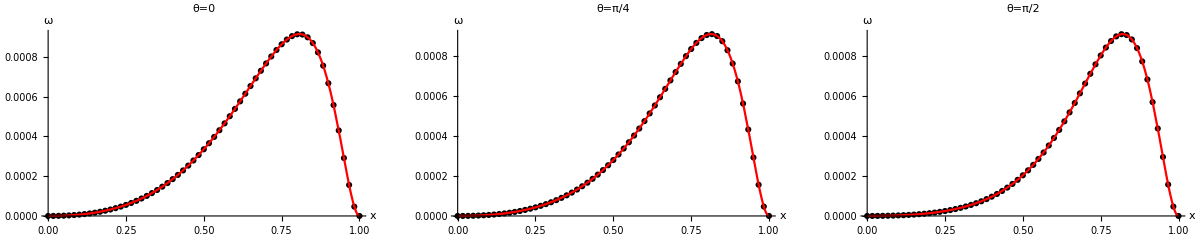

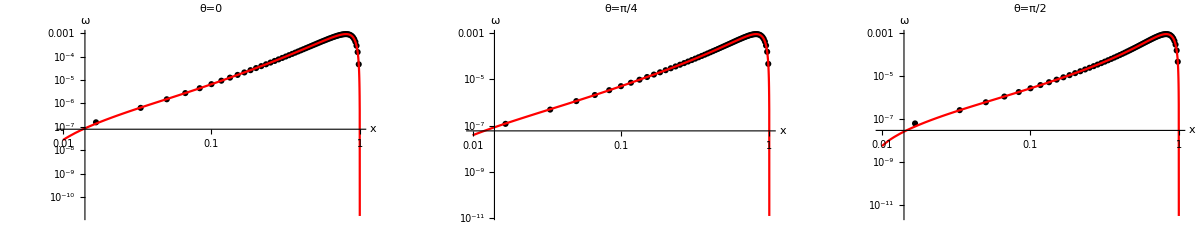

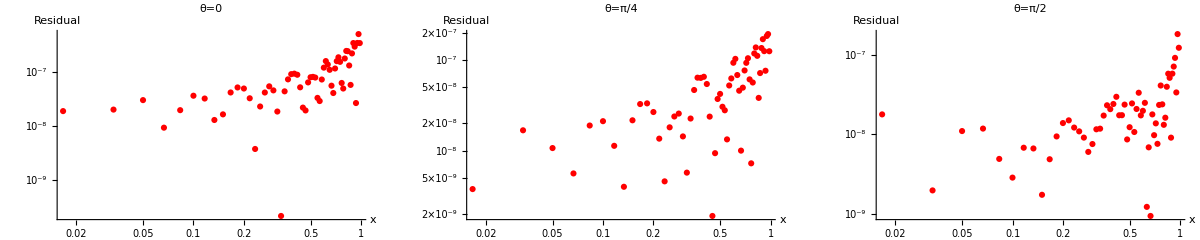

```mathematica
Show[GraphicsGrid[{{Show[u3Plot[[1;;2,1]],AxesLabel->{x,ω},PlotLabel->"θ=0",PlotRange->All],Show[u3Plot[[1;;2,2]],AxesLabel->{x,ω},PlotLabel->"θ=π/4",PlotRange->All],Show[u3Plot[[1;;2,3]],AxesLabel->{x,ω},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u3Plot[[3;;4,1]],AxesLabel->{x,ω},PlotLabel->"θ=0",PlotRange->All],Show[u3Plot[[3;;4,2]],AxesLabel->{x,ω},PlotLabel->"θ=π/4",PlotRange->All],Show[u3Plot[[3;;4,3]],AxesLabel->{x,ω},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u3Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u3Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u3Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

### ψ ζ^2 Fitting

#### y^n Order Determination: Local x(midpoint) location

{1}

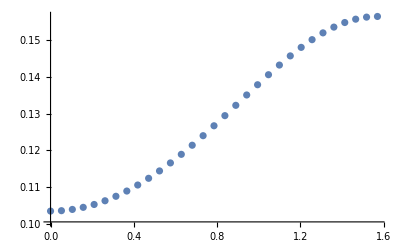

{0,2,4,6,8,10,12,14}

0.977816746932104

0.999912037612257

0.999999660207316

0.999999997662779

0.999999999463499

0.999999999543091

0.999999999530654

0.999999999557958

```mathematica
maxppos=Ordering[Abs[u4zeta2[[Length[Yrange],1;;]]],-1]
maxpYXdata=Transpose[{Ymat[[1;;,maxppos]]//Flatten,u4zeta2[[1;;,maxppos]]//Flatten}];
ListPlot[maxpYXdata]
yN={0,2,4,6,8,10,12,14}
Ynstr="yj LegendreP[j,Cos[y]]";
coeffn="{yj}";
Ftemp=0;
ctemp = {};
u4maxXFitFunc={};
u4maxXcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]];coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp; u4maxXFitFunc=Join[u4maxXFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u4maxXcoeffFitFunc=Join[u4maxXcoeffFitFunc,{ctemp}],{i,yN}]

u4maxXFit=Table[0,{i,Length[u4maxXFitFunc]}];
Do[u4maxXFit[[i]]=NonlinearModelFit[maxpYXdata,u4maxXFitFunc[[i]],u4maxXcoeffFitFunc[[i]],{y},PrecisionGoal->5,AccuracyGoal->5]; Print[NumberForm[u4maxXFit[[i]]["AdjustedRSquared"],16]],{i,Length[u4maxXFitFunc]}]
```

From this we notice that the R^2value saturates at n=8, with R^2=0.999999999463499

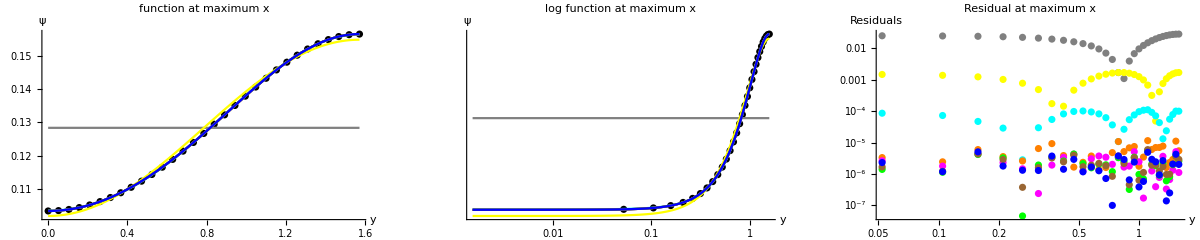

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
maxpXPlot=Table[0,{i,Length[u4maxXFit]+1}];
maxpXPlot[[1]]=ListPlot[maxpYXdata,PlotStyle->Black];
Do[maxpXPlot[[i+1]]=Plot[Normal[u4maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u4maxXFit]}]

maxpXLogPlot=Table[0,{i,Length[u4maxXFit]+1}];
maxpXLogPlot[[1]]=ListLogLogPlot[maxpYXdata,PlotStyle->Black];
Do[maxpXLogPlot[[i+1]]=LogLogPlot[Normal[u4maxXFit[[i]]],{y,Yrange[[1]],Yrange[[Length[Yrange]]]},PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u4maxXFit]}]

maxpXRes=Table[0,{i,Length[u4maxXFit]}];
Do[maxpXRes[[i]]=ListLogLogPlot[Transpose[{Ymat[[1;;,maxppos]]//Flatten,Abs[u4maxXFit[[i]]["FitResiduals"]]}],PlotStyle->Xcolors[[i+1]],PlotRange->All],{i,Length[u4maxXFit]}]


Show[GraphicsGrid[{{Show[maxpXPlot,AxesLabel->{y,ψ},PlotLabel->"function at maximum x",PlotRange->All], Show[maxpXLogPlot,AxesLabel->{y,ψ},PlotLabel->"log function at maximum x",PlotRange->All], Show[maxpXRes,AxesLabel->{y,"Residuals"},PlotLabel->"Residual at maximum x",PlotRange->All]}}],ImageSize->1200]
```

The magenta residuals on the right above plot correspond to r=8 which is roughly when the residual no longer improves by adding higher orders

#### x^n Order Determination (local y-fit): Order: y^8 (midpoint estimation)

```mathematica
xN={0,1,2,3,4,5,6,7,8,9,10,11,12,13} 
Ynstr="(LegendreP[0,Cos[y]] aj00 + LegendreP[2,Cos[y]] aj02 + LegendreP[4,Cos[y]] aj04 + LegendreP[6,Cos[y]] aj06 + LegendreP[8,Cos[y]] aj08)";
coeffn="{aj00,aj02,aj04,aj06,aj08}";
Xnstr="(-1+x) x^j";
Ftemp=0;
ctemp = {};
u4XFitFunc={};
u4XcoeffFitFunc={};
Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u4XFitFunc=Join[u4XFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u4XcoeffFitFunc=Join[u4XcoeffFitFunc,{ctemp}],{i,xN}]

u4XFit=Table[0,{i,Length[u4XFitFunc]}];
Do[u4XFit[[i]]=NonlinearModelFit[u4zeta2pts,u4XFitFunc[[i]],u4XcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u4XFit[[i]]["AdjustedRSquared"],16]],{i,Length[u4XFitFunc]}]
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13}

0.942809179284114

0.998350881463348

0.999956391149813

0.999979053306679

0.999994759622548

0.999999390188717

0.999999968142122

0.99999999333855

0.99999999577742

0.999999998389117

0.999999999287923

0.999999999467985

0.99999999948849

0.999999999489129

Here n=10

{1,16,31}

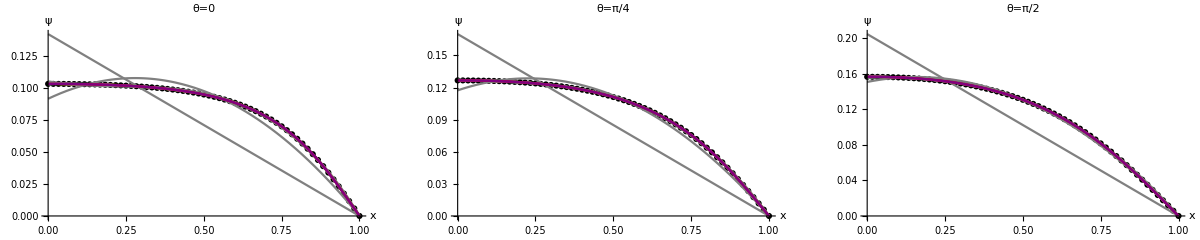

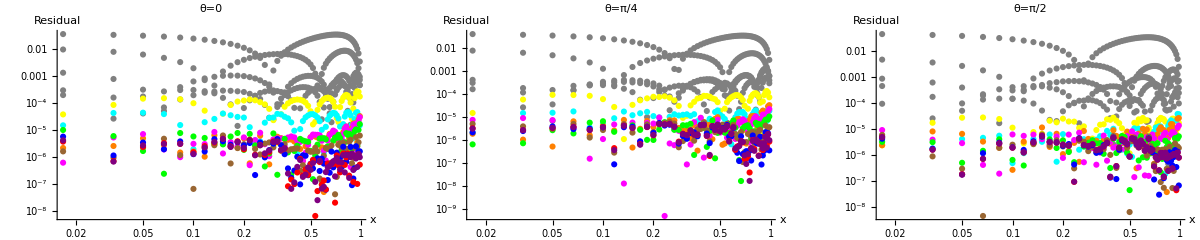

```mathematica
Xcolors={Black,Gray,Gray,Gray,Gray,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u4XPlotY=Table[0,{i,Length[u4XFit]+1},{j,Length[Yplot]}];
Do[u4XPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u4zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u4XPlotY[[i+1,j]]=Plot[u4XFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u4XFit]}]
Show[GraphicsGrid[{{Show[u4XPlotY[[1;;,1]],AxesLabel->{x,ψ},PlotLabel->"θ=0",PlotRange->All],Show[u4XPlotY[[1;;,2]],AxesLabel->{x,ψ},PlotLabel->"θ=π/4",PlotRange->All],Show[u4XPlotY[[1;;,3]],AxesLabel->{x,ψ},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u4XFitRes=Table[0,{i,Length[u4XFit]}];
Do[u4XFitRes[[i]]=Partition[u4XFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u4XFit]}]
u4XResY=Table[0,{i,Length[u4XFit]},{j,Length[Yplot]}];

Do[Do[u4XResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u4XFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u4XFit]}]
Show[GraphicsGrid[{{Show[u4XResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u4XResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u4XResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

Visual verification on bottom-right plot where n=10 is the brown residual

#### y^n Order Determination (global x-fit): Order: x^10

```mathematica
yN={0,2,4,6,8,10,12}
Xnstr="(-1+x)(a00j + x^1 a01j + x^2 a02j + x^3 a03j + x^4 a04j + x^5 a05j + x^6 a06j + x^7 a07j + x^8 a08j + x^9 a09j + x^(10) a10j)";
coeffn="{a00j,a01j,a02j,a03j,a04j,a05j,a06j,a07j,a08j,a09j,a10j}";
Ynstr="LegendreP[j,Cos[y]]";
Ftemp=0;
ctemp = {};
u4YFitFunc={};
u4YcoeffFitFunc={};

Do[ytemp=ToExpression[StringReplace[Ynstr,ToString[j]->IntegerString[i,10,2]]]; xtemp=ToExpression[StringReplace[Xnstr,ToString[j]->IntegerString[i,10,2]]]; coefftemp=ToExpression[StringReplace[coeffn,ToString[j]->IntegerString[i,10,2]]]; Ftemp=Ftemp+ytemp*xtemp; u4YFitFunc=Join[u4YFitFunc,{Ftemp}]; ctemp=Join[ctemp,coefftemp];u4YcoeffFitFunc=Join[u4YcoeffFitFunc,{ctemp}],{i,yN}]
(* To switch between x^n and y^n,  switch u#X... to u#Y... and change Do[...,{i,xN}] to Do[...,{i,yN}] *)

u4YFit=Table[0,{i,Length[u4YFitFunc]}];
Do[u4YFit[[i]]=NonlinearModelFit[u4zeta2pts,u4YFitFunc[[i]],u4YcoeffFitFunc[[i]],{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)]; Print[NumberForm[u4YFit[[i]]["AdjustedRSquared"],16]],{i,Length[u4YFitFunc]}]
```

{0,2,4,6,8,10,12}

0.98411738281126

0.999948142125193

0.999999831151114

0.99999999856049

0.999999999287923

0.999999999294566

0.999999999295238

This is just verification, we determined y^8 was the saturation point only from a fit at the location where u_0 was maximum. So in that case we had a 1-dimensional fit to make. In this case, we find the y^n value for a global fit on the x-dimension. We recover that the saturation residual is again n=8

{1,16,31}

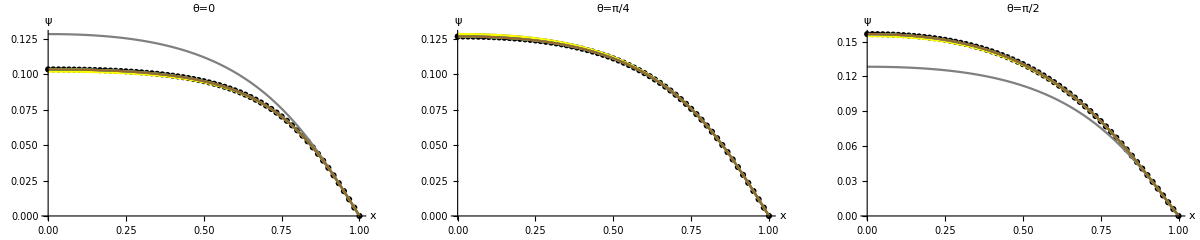

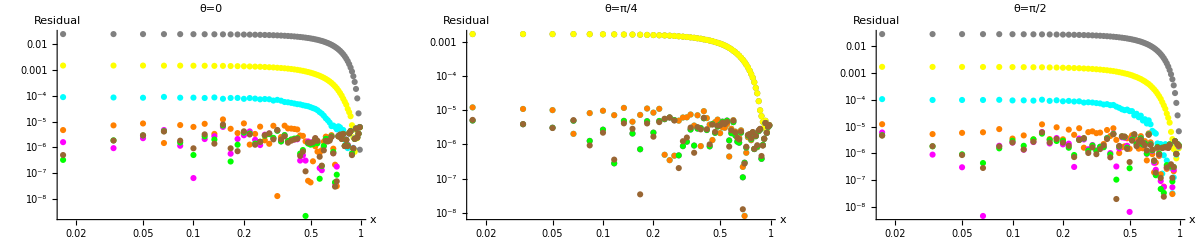

```mathematica
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]}

u4YPlotY=Table[0,{i,Length[u4YFit]+1},{j,Length[Yplot]}];
Do[u4YPlotY[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u4zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];

Do[Do[u4YPlotY[[i+1,j]]=Plot[u4YFit[[i]]["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u4YFit]}]
Show[GraphicsGrid[{{Show[u4YPlotY[[1;;,1]],AxesLabel->{x,ψ},PlotLabel->"θ=0",PlotRange->All],Show[u4YPlotY[[1;;,2]],AxesLabel->{x,ψ},PlotLabel->"θ=π/4",PlotRange->All],Show[u4YPlotY[[1;;,3]],AxesLabel->{x,ψ},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

u4YFitRes=Table[0,{i,Length[u4YFit]}];
Do[u4YFitRes[[i]]=Partition[u4YFit[[i]]["FitResiduals"],Length[Xrange]],{i,Length[u4YFit]}]
u4YResY=Table[0,{i,Length[u4YFit]},{j,Length[Yplot]}];
Do[Do[u4YResY[[i,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u4YFitRes[[i]][[Yplot[[j]],1;;]]]}],PlotStyle->Xcolors[[i+1]]],{j,Length[Yplot]}],{i,Length[u4YFit]}]

Show[GraphicsGrid[{{Show[u4YResY[[1;;,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All], Show[u4YResY[[1;;,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All], Show[u4YResY[[1;;,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

As explained above, n=8 is the magenta residual

#### Best Fit Calculation: Order: P_8, x^10, u4YFitFunc[[5]]

```mathematica
u4FitFunc=u4YFitFunc[[5]]
u4coeffFitFunc=u4YcoeffFitFunc[[5]];
fullu4fit=NonlinearModelFit[u4zeta2pts,u4FitFunc,u4coeffFitFunc,{y,x},PrecisionGoal->5,AccuracyGoal->5,Weights->1/error^2,VarianceEstimatorFunction->(1&)];
Normal[fullu4fit];
fullu4fit["BestFitParameters"]
NumberForm[fullu4fit["AdjustedRSquared"],16]
fullu4fit["ParameterTable"];
fullu4fit["ANOVATable"]
```

(-1+x) (a0000+a0100 x+a0200 x^2+a0300 x^3+a0400 x^4+a0500 x^5+a0600 x^6+a0700 x^7+a0800 x^8+a0900 x^9+a1000 x^10)+1/2 (-1+x) (a0002+a0102 x+a0202 x^2+a0302 x^3+a0402 x^4+a0502 x^5+a0602 x^6+a0702 x^7+a0802 x^8+a0902 x^9+a1002 x^10) (-1+3 Cos[y]^2)+1/8 (-1+x) (a0004+a0104 x+a0204 x^2+a0304 x^3+a0404 x^4+a0504 x^5+a0604 x^6+a0704 x^7+a0804 x^8+a0904 x^9+a1004 x^10) (3-30 Cos[y]^2+35 Cos[y]^4)+1/16 (-1+x) (a0006+a0106 x+a0206 x^2+a0306 x^3+a0406 x^4+a0506 x^5+a0606 x^6+a0706 x^7+a0806 x^8+a0906 x^9+a1006 x^10) (-5+105 Cos[y]^2-315 Cos[y]^4+231 Cos[y]^6)+1/128 (-1+x) (a0008+a0108 x+a0208 x^2+a0308 x^3+a0408 x^4+a0508 x^5+a0608 x^6+a0708 x^7+a0808 x^8+a0908 x^9+a1008 x^10) (35-1260 Cos[y]^2+6930 Cos[y]^4-12012 Cos[y]^6+6435 Cos[y]^8)

{a0000→-0.137025,a0100→-0.13673,a0200→-0.106437,a0300→0.172599,a0400→-1.88013,a0500→8.90033,a0600→-25.7303,a0700→45.8576,a0800→-49.1069,a0900→29.0233,a1000→-7.20873,a0002→0.0364423,a0102→0.0368755,a0202→-0.0117068,a0302→0.226266,a0402→-1.9928,a0502→8.69758,a0602→-23.9179,a0702→40.4685,a0802→-41.3201,a0902→23.1701,a1002→-5.39285,a0004→-0.00309129,a0104→-0.00311153,a0204→0.00267388,a0304→-0.0170016,a0404→0.16696,a0504→-0.627251,a0604→1.49435,a0704→-2.2313,a0804→2.07764,a0904→-1.15123,a1004→0.291438,a0006→0.000230482,a0106→0.000169571,a0206→-0.00063843,a0306→0.0201126,a0406→-0.20381,a0506→0.960763,a0606→-2.59733,a0706→4.21522,a0806→-4.04929,a0906→2.12325,a1006→-0.468717,a0008→-0.000018167,a0108→0.0000370657,a0208→-0.00118974,a0308→0.0114577,a0408→-0.0525874,a0508→0.117529,a0608→-0.0721248,a0708→-0.200381,a0808→0.44758,a0908→-0.349316,a1008→0.0990391}

0.999999999287923

General::munfl: Exp[-13638.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5310.66] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-9977.37] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

| DF | SS | MS
Model | 55 | 2.02262×10^11 | 3.67749×10^9
Error | 1836 | 139.837 | 0.076164
Uncorrected Total | 1891 | 2.02262×10^11 | 
Corrected Total | 1890 | 2.90571×10^10 |

#### Best Fit Comparison

```mathematica
u4fitres=Partition[fullu4fit["FitResiduals"],Length[Xrange]];
Xcolors={Black,Gray,Yellow,Cyan,Orange,Magenta,Green,Brown,Blue,Red,Purple};
Yplot={1,(Length[Yrange]+1)/2,Length[Yrange]};
u4Plot=Table[0,5,{i,Length[Yplot]}];

Do[u4Plot[[1,j]]=ListPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],u4zeta2[[Yplot[[j]],1;;]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u4Plot[[2,j]]=Plot[fullu4fit["Function"][Yrange[[Yplot[[j]]]],x],{x,0,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u4Plot[[3,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u4zeta2[[Yplot[[j]],1;;]]]}],PlotStyle->Black],{j,Length[Yplot]}];
Do[u4Plot[[4,j]]=LogLogPlot[Abs[fullu4fit["Function"][Yrange[[Yplot[[j]]]],x]],{x,0.01,1},PlotStyle->Red],{j,Length[Yplot]}];
Do[u4Plot[[5,j]]=ListLogLogPlot[Transpose[{Xmat[[Yplot[[j]],1;;]],Abs[u4fitres[[Yplot[[j]],1;;]]]}],PlotStyle->Red],{j,Length[Yplot]}];
```

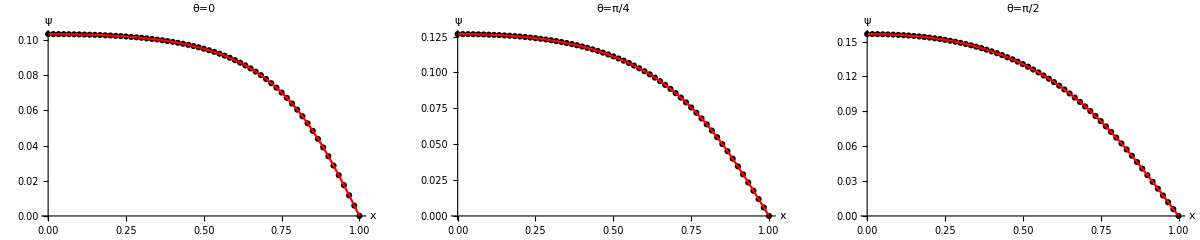

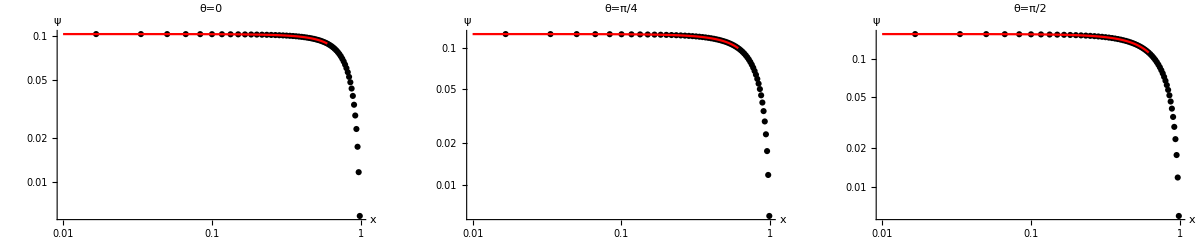

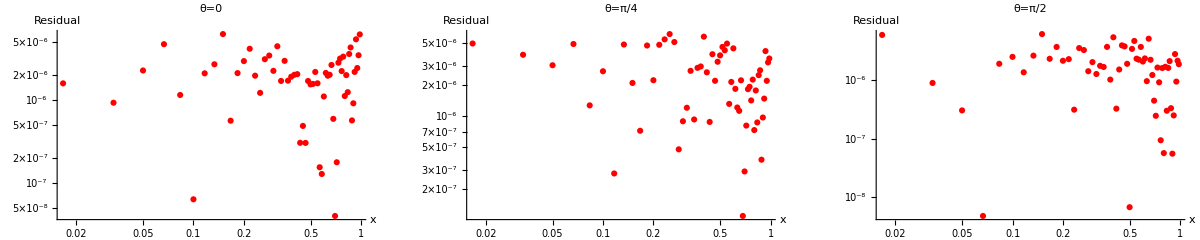

```mathematica
Show[GraphicsGrid[{{Show[u4Plot[[1;;2,1]],AxesLabel->{x,ψ},PlotLabel->"θ=0",PlotRange->All],Show[u4Plot[[1;;2,2]],AxesLabel->{x,ψ},PlotLabel->"θ=π/4",PlotRange->All],Show[u4Plot[[1;;2,3]],AxesLabel->{x,ψ},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u4Plot[[3;;4,1]],AxesLabel->{x,ψ},PlotLabel->"θ=0",PlotRange->All],Show[u4Plot[[3;;4,2]],AxesLabel->{x,ψ},PlotLabel->"θ=π/4",PlotRange->All],Show[u4Plot[[3;;4,3]],AxesLabel->{x,ψ},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]

Show[GraphicsGrid[{{Show[u4Plot[[5,1]],AxesLabel->{x,"Residual"},PlotLabel->"θ=0",PlotRange->All],Show[u4Plot[[5,2]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/4",PlotRange->All],Show[u4Plot[[5,3]],AxesLabel->{x,"Residual"},PlotLabel->"θ=π/2",PlotRange->All]}}],ImageSize->1200]
```

## Export

### Fit export

```mathematica
Export["LinearFitXmatout.dat",Transpose[Xmat]];
Export["LinearFitYmatout.dat",Transpose[Ymat]];
Export["LinearFitu0out.dat",Transpose[fullu0fit["Function"][Ymat,Xmat]]];
Export["LinearFitu1out.dat",Transpose[fullu1fit["Function"][Ymat,Xmat]]];
Export["LinearFitu2out.dat",Transpose[fullu2fit["Function"][Ymat,Xmat]]];
Export["LinearFitu3out.dat",Transpose[fullu3fit["Function"][Ymat,Xmat]]];
Export["LinearFitu4out.dat",Transpose[fullu4fit["Function"][Ymat,Xmat]]];

Export["LinearFitout.dat",Transpose[{Xmat[[Yplot[[1]],1;;]],
u0zeta2[[Yplot[[1]],1;;]],fullu0fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u0fitres[[Yplot[[1]],1;;]]],
u1zeta2[[Yplot[[1]],1;;]],fullu1fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u1fitres[[Yplot[[1]],1;;]]],
u2zeta2[[Yplot[[1]],1;;]],fullu2fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u2fitres[[Yplot[[1]],1;;]]],
u3zeta2[[Yplot[[1]],1;;]],fullu3fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u3fitres[[Yplot[[1]],1;;]]],
u4zeta2[[Yplot[[1]],1;;]],fullu4fit["Function"][Yrange[[Yplot[[1]]]],Xmat[[Yplot[[1]],1;;]]],
Abs[u4fitres[[Yplot[[1]],1;;]]],
u0zeta2[[Yplot[[2]],1;;]],fullu0fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u0fitres[[Yplot[[2]],1;;]]],
u1zeta2[[Yplot[[2]],1;;]],fullu1fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u1fitres[[Yplot[[2]],1;;]]],
u2zeta2[[Yplot[[2]],1;;]],fullu2fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u2fitres[[Yplot[[2]],1;;]]],
u3zeta2[[Yplot[[2]],1;;]],fullu3fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u3fitres[[Yplot[[2]],1;;]]],
u4zeta2[[Yplot[[2]],1;;]],fullu4fit["Function"][Yrange[[Yplot[[2]]]],Xmat[[Yplot[[2]],1;;]]],
Abs[u4fitres[[Yplot[[2]],1;;]]],
u0zeta2[[Yplot[[3]],1;;]],fullu0fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u0fitres[[Yplot[[3]],1;;]]],
u1zeta2[[Yplot[[3]],1;;]],fullu1fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u1fitres[[Yplot[[3]],1;;]]],
u2zeta2[[Yplot[[3]],1;;]],fullu2fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u2fitres[[Yplot[[3]],1;;]]],
u3zeta2[[Yplot[[3]],1;;]],fullu3fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u3fitres[[Yplot[[3]],1;;]]],
u4zeta2[[Yplot[[3]],1;;]],fullu4fit["Function"][Yrange[[Yplot[[3]]]],Xmat[[Yplot[[3]],1;;]]],
Abs[u4fitres[[Yplot[[3]],1;;]]]}]];
```

## Fit Export

```mathematica
LINu0export=fullu0fit["BestFitParameters"];
LINu1export=fullu1fit["BestFitParameters"];
LINu2export=fullu2fit["BestFitParameters"];
LINu3export=fullu3fit["BestFitParameters"];
LINu4export=fullu4fit["BestFitParameters"];

For[i=1,i<=Length[LINu1export],i++,LINu1export[[i]]=ToExpression[StringReplace[ToString[LINu1export[[i]],FormatType->StandardForm],"a"->"b"]]]

For[i=1,i<=Length[LINu2export],i++,LINu2export[[i]]=ToExpression[StringReplace[ToString[LINu2export[[i]],FormatType->StandardForm],"a"->"c"]]]

For[i=1,i<=Length[LINu3export],i++,LINu3export[[i]]=ToExpression[StringReplace[ToString[LINu3export[[i]],FormatType->StandardForm],"a"->"d"]]]

For[i=1,i<=Length[LINu4export],i++,LINu4export[[i]]=ToExpression[StringReplace[ToString[LINu4export[[i]],FormatType->StandardForm],"a"->"e"]]]
```

```mathematica
Export["LINu0FitCoeffs.mx",LINu0export]
Export["LINu1FitCoeffs.mx",LINu1export]
Export["LINu2FitCoeffs.mx",LINu2export]
Export["LINu3FitCoeffs.mx",LINu3export]
Export["LINu4FitCoeffs.mx",LINu4export]
```

LINu0FitCoeffs.mx

LINu1FitCoeffs.mx

LINu2FitCoeffs.mx

LINu3FitCoeffs.mx

LINu4FitCoeffs.mx

```mathematica
Import["LINu0FitCoeffs.mx"]
Import["LINu1FitCoeffs.mx"]
Import["LINu2FitCoeffs.mx"]
Import["LINu3FitCoeffs.mx"]
Import["LINu4FitCoeffs.mx"]
```

{a0000→0.00192074,a0100→-0.00699936,a0200→0.222238,a0300→-2.43508,a0400→17.0928,a0500→-78.8656,a0600→249.522,a0700→-549.395,a0800→841.615,a0900→-879.628,a1000→598.17,a1100→-238.469,a1200→42.2355,a0002→-0.000410087,a0102→-0.00342314,a0202→0.0502261,a0302→-0.581984,a0402→4.00264,a0502→-18.2084,a0602→56.4184,a0702→-121.016,a0802→179.314,a0902→-179.616,a1002→115.617,a1102→-42.8566,a1202→6.88074,a0004→0.000125505,a0104→-0.000151604,a0204→0.0073039,a0304→-0.0717064,a0404→0.44672,a0504→-1.84563,a0604→5.22227,a0704→-10.2927,a0804→14.0973,a0904→-13.1427,a1004→7.9385,a1104→-2.78991,a1204→0.430614,a0006→-0.000022434,a0106→0.000440395,a0206→-0.00927602,a0306→0.099498,a0406→-0.654855,a0506→2.82505,a0606→-8.27782,a0706→16.7569,a0806→-23.4395,a0906→22.2415,a1006→-13.6688,a1106→4.9095,a1206→-0.782661}

{b0000→-0.0237399,b0100→-0.0185324,b0200→-0.105798,b0300→0.618027,b0400→-3.18734,b0500→9.59926,b0600→-18.5792,b0700→22.0823,b0800→-14.8822,b0900→4.37689,b0002→0.0214391,b0102→0.0222073,b0202→0.00453542,b0302→0.103203,b0402→-0.41899,b0502→1.18179,b0602→-1.95355,b0702→1.84455,b0802→-0.829193,b0902→0.08561,b0004→-0.00406999,b0104→-0.00696562,b0204→0.0400924,b0304→-0.264758,b0404→1.14006,b0504→-2.86526,b0604→4.46302,b0704→-4.08713,b0804→1.93934,b0904→-0.354087,b0006→0.000409539,b0106→0.000672215,b0206→-0.00384938,b0306→0.0238379,b0406→-0.112017,b0506→0.309759,b0606→-0.548627,b0706→0.597233,b0806→-0.3524,b0906→0.0849664,b0008→-0.0000441697,b0108→0.000271125,b0208→-0.00434781,b0308→0.0324583,b0408→-0.135987,b0508→0.347201,b0608→-0.543763,b0708→0.507702,b0808→-0.259166,b0908→0.0556765}

{c0000→-0.00300347,c0100→-0.00804232,c0200→0.051956,c0300→-0.480631,c0400→1.80308,c0500→-4.43508,c0600→6.32362,c0700→-5.02722,c0800→1.7153,c0002→-0.00314546,c0102→-0.0220233,c0202→0.225757,c0302→-1.3572,c0402→4.95328,c0502→-10.6422,c0602→13.5783,c0702→-9.44789,c0802→2.71531,c0004→0.00119522,c0104→-0.00155691,c0204→0.0284979,c0304→-0.17656,c0404→0.560461,c0504→-1.07779,c0604→1.17368,c0704→-0.637146,c0804→0.128973,c0006→-0.000184623,c0106→0.000164718,c0206→-0.00387708,c0306→0.0272584,c0406→-0.0962599,c0506→0.209957,c0606→-0.268032,c0706→0.17882,c0806→-0.047858,c0008→0.0000167729,c0108→0.000117422,c0208→-0.00111638,c0308→0.00589835,c0408→-0.0189994,c0508→0.0345527,c0608→-0.0348358,c0708→0.0182139,c0808→-0.00384255}

{d0000→-9.1781×10^-10,d0100→-2.7153×10^-6,d0200→0.000569712,d0300→-0.0045254,d0400→0.0774893,d0500→-0.507938,d0600→2.11964,d0700→-5.28002,d0800→8.00157,d0900→-6.71128,d1000→2.50702,d0002→-1.02465×10^-8,d0102→3.5766×10^-7,d0202→0.000320516,d0302→-0.00286885,d0402→0.0571903,d0502→-0.40583,d0602→1.70841,d0702→-4.216,d0802→6.09466,d0902→-4.76497,d1002→1.53169,d0004→1.09597×10^-8,d0104→-4.70409×10^-6,d0204→0.00019467,d0304→-0.00420979,d0404→0.0367874,d0504→-0.190593,d0604→0.587247,d0704→-1.10352,d0804→1.22889,d0904→-0.735085,d1004→0.180224,d0006→-2.79842×10^-11,d0106→3.91608×10^-8,d0206→3.58331×10^-7,d0306→0.0000723982,d0406→-0.000650564,d0506→0.0041597,d0606→-0.0151773,d0706→0.0335359,d0806→-0.0440952,d0906→0.0310158,d1006→-0.00886592}

{e0000→-0.137025,e0100→-0.13673,e0200→-0.106437,e0300→0.172599,e0400→-1.88013,e0500→8.90033,e0600→-25.7303,e0700→45.8576,e0800→-49.1069,e0900→29.0233,e1000→-7.20873,e0002→0.0364423,e0102→0.0368755,e0202→-0.0117068,e0302→0.226266,e0402→-1.9928,e0502→8.69758,e0602→-23.9179,e0702→40.4685,e0802→-41.3201,e0902→23.1701,e1002→-5.39285,e0004→-0.00309129,e0104→-0.00311153,e0204→0.00267388,e0304→-0.0170016,e0404→0.16696,e0504→-0.627251,e0604→1.49435,e0704→-2.2313,e0804→2.07764,e0904→-1.15123,e1004→0.291438,e0006→0.000230482,e0106→0.000169571,e0206→-0.00063843,e0306→0.0201126,e0406→-0.20381,e0506→0.960763,e0606→-2.59733,e0706→4.21522,e0806→-4.04929,e0906→2.12325,e1006→-0.468717,e0008→-0.000018167,e0108→0.0000370657,e0208→-0.00118974,e0308→0.0114577,e0408→-0.0525874,e0508→0.117529,e0608→-0.0721248,e0708→-0.200381,e0808→0.44758,e0908→-0.349316,e1008→0.0990391}